```mathematica
Table[allGraphs5[k,"colofournull"],{k,allGraphs5FakeAtomKeys}]
```

{p1x2x3x4x5,p12x3x4x5,p12345,p1234x5,p1235x4,p123x4x5,p123x45,p1245x3,p124x3x5,p124x35,p125x3x4,p125x34,p12x34x5,p12x345,p12x35x4,p12x3x45,p13x2x4x5,p1345x2,p134x25,p134x2x5,p135x24,p135x2x4,p13x24x5,p13x245,p13x25x4,p13x2x45,p14x2x3x5,p145x23,p145x2x3,p14x23x5,p14x235,p14x25x3,p14x2x35,p15x2x3x4,p15x23x4,p15x234,p15x24x3,p15x2x34,p1x23x4x5,p1x2345,p1x234x5,p1x235x4,p1x23x45,p1x24x3x5,p1x245x3,p1x24x35,p1x25x3x4,p1x25x34,p1x2x34x5,p1x2x345,p1x2x35x4,p1x2x3x45}

```mathematica
Table[allGraphs5[k,"colofour"],{k,allGraphs5AtomKeys}]
```

{v1x2x3x4x5,v1x2x3x45,v1x2x35x4,v1x2x34x5,v1x2x345,v1x25x3x4,v1x25x34,v1x24x3x5,v1x24x35,v1x245x3,v1x23x4x5,v1x23x45,v1x235x4,v1x234x5,v1x2345,v15x2x3x4,v15x2x34,v15x24x3,v15x23x4,v15x234,v14x2x3x5,v14x2x35,v14x25x3,v14x23x5,v14x235,v145x2x3,v145x23,v13x2x4x5,v13x2x45,v13x25x4,v13x24x5,v13x245,v135x2x4,v135x24,v134x2x5,v134x25,v1345x2,v12x3x4x5,v12x3x45,v12x35x4,v12x34x5,v12x345,v125x3x4,v125x34,v124x3x5,v124x35,v1245x3,v123x4x5,v123x45,v1235x4,v1234x5,v12345}

```mathematica
fakeAtoms=Sort[Table[allGraphs5[k,"colofournull"],{k,allGraphs5FakeAtomKeys}],CompareSymbols[#1,#2]&]
```

{p1x2x3x4x5,p1x2x3x45,p1x2x34x5,p1x2x35x4,p1x23x4x5,p1x24x3x5,p1x25x3x4,p12x3x4x5,p13x2x4x5,p14x2x3x5,p15x2x3x4,p1x23x45,p1x24x35,p1x25x34,p12x3x45,p12x34x5,p12x35x4,p13x2x45,p13x24x5,p13x25x4,p14x2x35,p14x23x5,p14x25x3,p15x2x34,p15x23x4,p15x24x3,p1x2x345,p1x234x5,p1x235x4,p1x245x3,p123x4x5,p124x3x5,p125x3x4,p134x2x5,p135x2x4,p145x2x3,p12x345,p123x45,p124x35,p125x34,p13x245,p134x25,p135x24,p14x235,p145x23,p15x234,p1x2345,p1234x5,p1235x4,p1245x3,p1345x2,p12345}

```mathematica
fakeCoeff[exp_]:=Table[Coefficient[exp,k],{k,fakeAtoms}]
```

```mathematica
sols=Sort[Solve[Table[allGraphs5[k,"colofournull"]==allGraphs5[k,"colofour"],{k,allGraphs5FakeAtomKeys}],Table[allGraphs5[k,"colofour"],{k,allGraphs5AtomKeys}]],CompareSymbols[#1[[1]],#2[[1]] ]&]
```

{{v1x2x3x4x5→p12345,v1x2x3x45→1/12 (-3 p12345+3 p1234x5+3 p1235x4-9 p123x45+6 p123x4x5-p1245x3+3 p124x35-2 p124x3x5+3 p125x34-2 p125x3x4-3 p12x345+4 p12x3x45-2 p12x3x4x5-p1345x2+3 p134x25-2 p134x2x5+3 p135x24-2 p135x2x4-3 p13x245+4 p13x2x45-2 p13x2x4x5-3 p145x23+2 p145x2x3+3 p14x235-2 p14x25x3-2 p14x2x35+2 p14x2x3x5+3 p15x234-2 p15x24x3-2 p15x2x34+2 p15x2x3x4-p1x2345-2 p1x234x5-2 p1x235x4+4 p1x23x45-2 p1x23x4x5+2 p1x245x3-2 p1x24x35+2 p1x24x3x5-2 p1x25x34+2 p1x25x3x4+2 p1x2x345+2 p1x2x34x5+2 p1x2x35x4-6 p1x2x3x45),v1x2x35x4→1/12 (-3 p12345+3 p1234x5-p1235x4+3 p123x45-2 p123x4x5+3 p1245x3-9 p124x35+6 p124x3x5+3 p125x34-2 p125x3x4-3 p12x345+4 p12x35x4-2 p12x3x4x5-p1345x2+3 p134x25-2 p134x2x5-3 p135x24+2 p135x2x4+3 p13x245-2 p13x25x4-2 p13x2x45+2 p13x2x4x5+3 p145x23-2 p145x2x3-3 p14x235+4 p14x2x35-2 p14x2x3x5+3 p15x234-2 p15x23x4-2 p15x2x34+2 p15x2x3x4-p1x2345-2 p1x234x5+2 p1x235x4-2 p1x23x45+2 p1x23x4x5-2 p1x245x3+4 p1x24x35-2 p1x24x3x5-2 p1x25x34+2 p1x25x3x4+2 p1x2x345+2 p1x2x34x5-6 p1x2x35x4+2 p1x2x3x45),v1x2x34x5→1/12 (-3 p12345-p1234x5+3 p1235x4+3 p123x45-2 p123x4x5+3 p1245x3+3 p124x35-2 p124x3x5-9 p125x34+6 p125x3x4-3 p12x345+4 p12x34x5-2 p12x3x4x5-p1345x2-3 p134x25+2 p134x2x5+3 p135x24-2 p135x2x4+3 p13x245-2 p13x24x5-2 p13x2x45+2 p13x2x4x5+3 p145x23-2 p145x2x3+3 p14x235-2 p14x23x5-2 p14x2x35+2 p14x2x3x5-3 p15x234+4 p15x2x34-2 p15x2x3x4-p1x2345+2 p1x234x5-2 p1x235x4-2 p1x23x45+2 p1x23x4x5-2 p1x245x3-2 p1x24x35+2 p1x24x3x5+4 p1x25x34-2 p1x25x3x4+2 p1x2x345-6 p1x2x34x5+2 p1x2x35x4+2 p1x2x3x45),v1x2x345→1/12 (p12345-p1234x5-p1235x4-p123x45+2 p123x4x5-p1245x3-p124x35+2 p124x3x5-p125x34+2 p125x3x4+5 p12x345-4 p12x34x5-4 p12x35x4-4 p12x3x45+6 p12x3x4x5+p1345x2-p134x25-p135x24-p13x245+2 p13x24x5+2 p13x25x4-2 p13x2x4x5-p145x23-p14x235+2 p14x23x5+2 p14x25x3-2 p14x2x3x5-p15x234+2 p15x23x4+2 p15x24x3-2 p15x2x3x4+p1x2345-2 p1x23x4x5-2 p1x24x3x5-2 p1x25x3x4-2 p1x2x345+2 p1x2x34x5+2 p1x2x35x4+2 p1x2x3x45),v1x25x3x4→1/12 (-3 p12345+3 p1234x5-p1235x4+3 p123x45-2 p123x4x5-p1245x3+3 p124x35-2 p124x3x5-3 p125x34+2 p125x3x4+3 p12x345-2 p12x35x4-2 p12x3x45+2 p12x3x4x5+3 p1345x2-9 p134x25+6 p134x2x5+3 p135x24-2 p135x2x4-3 p13x245+4 p13x25x4-2 p13x2x4x5+3 p145x23-2 p145x2x3-3 p14x235+4 p14x25x3-2 p14x2x3x5+3 p15x234-2 p15x23x4-2 p15x24x3+2 p15x2x3x4-p1x2345-2 p1x234x5+2 p1x235x4-2 p1x23x45+2 p1x23x4x5+2 p1x245x3-2 p1x24x35+2 p1x24x3x5+4 p1x25x34-6 p1x25x3x4-2 p1x2x345-2 p1x2x34x5+2 p1x2x35x4+2 p1x2x3x45),v1x25x34→1/12 (p12345-p1234x5-p1235x4-p123x45+2 p123x4x5-p1245x3-p124x35+2 p124x3x5+5 p125x34-4 p125x3x4-p12x345-4 p12x34x5+2 p12x35x4+2 p12x3x45-p1345x2+5 p134x25-4 p134x2x5-p135x24+2 p135x2x4-p13x245+2 p13x24x5-4 p13x25x4+2 p13x2x45-p145x23+2 p145x2x3-p14x235+2 p14x23x5-4 p14x25x3+2 p14x2x35-p15x234+2 p15x23x4+2 p15x24x3-4 p15x2x34+p1x2345-2 p1x23x4x5-2 p1x24x3x5+4 p1x25x3x4+4 p1x2x34x5-2 p1x2x35x4-2 p1x2x3x45),v1x24x3x5→1/12 (-3 p12345-p1234x5+3 p1235x4+3 p123x45-2 p123x4x5-p1245x3-3 p124x35+2 p124x3x5+3 p125x34-2 p125x3x4+3 p12x345-2 p12x34x5-2 p12x3x45+2 p12x3x4x5+3 p1345x2+3 p134x25-2 p134x2x5-9 p135x24+6 p135x2x4-3 p13x245+4 p13x24x5-2 p13x2x4x5+3 p145x23-2 p145x2x3+3 p14x235-2 p14x23x5-2 p14x25x3+2 p14x2x3x5-3 p15x234+4 p15x24x3-2 p15x2x3x4-p1x2345+2 p1x234x5-2 p1x235x4-2 p1x23x45+2 p1x23x4x5+2 p1x245x3+4 p1x24x35-6 p1x24x3x5-2 p1x25x34+2 p1x25x3x4-2 p1x2x345+2 p1x2x34x5-2 p1x2x35x4+2 p1x2x3x45),v1x24x35→1/12 (p12345-p1234x5-p1235x4-p123x45+2 p123x4x5-p1245x3+5 p124x35-4 p124x3x5-p125x34+2 p125x3x4-p12x345+2 p12x34x5-4 p12x35x4+2 p12x3x45-p1345x2-p134x25+2 p134x2x5+5 p135x24-4 p135x2x4-p13x245-4 p13x24x5+2 p13x25x4+2 p13x2x45-p145x23+2 p145x2x3-p14x235+2 p14x23x5+2 p14x25x3-4 p14x2x35-p15x234+2 p15x23x4-4 p15x24x3+2 p15x2x34+p1x2345-2 p1x23x4x5+4 p1x24x3x5-2 p1x25x3x4-2 p1x2x34x5+4 p1x2x35x4-2 p1x2x3x45),v1x245x3→1/12 (p12345-p1234x5-p1235x4-p123x45+2 p123x4x5+p1245x3-p124x35-p125x34-p12x345+2 p12x34x5+2 p12x35x4-2 p12x3x4x5-p1345x2-p134x25+2 p134x2x5-p135x24+2 p135x2x4+5 p13x245-4 p13x24x5-4 p13x25x4-4 p13x2x45+6 p13x2x4x5-p145x23-p14x235+2 p14x23x5+2 p14x2x35-2 p14x2x3x5-p15x234+2 p15x23x4+2 p15x2x34-2 p15x2x3x4+p1x2345-2 p1x23x4x5-2 p1x245x3+2 p1x24x3x5+2 p1x25x3x4-2 p1x2x34x5-2 p1x2x35x4+2 p1x2x3x45),v1x23x4x5→1/12 (-3 p12345-p1234x5-p1235x4-3 p123x45+2 p123x4x5+3 p1245x3+3 p124x35-2 p124x3x5+3 p125x34-2 p125x3x4+3 p12x345-2 p12x34x5-2 p12x35x4+2 p12x3x4x5+3 p1345x2+3 p134x25-2 p134x2x5+3 p135x24-2 p135x2x4+3 p13x245-2 p13x24x5-2 p13x25x4+2 p13x2x4x5-9 p145x23+6 p145x2x3-3 p14x235+4 p14x23x5-2 p14x2x3x5-3 p15x234+4 p15x23x4-2 p15x2x3x4-p1x2345+2 p1x234x5+2 p1x235x4+4 p1x23x45-6 p1x23x4x5-2 p1x245x3-2 p1x24x35+2 p1x24x3x5-2 p1x25x34+2 p1x25x3x4-2 p1x2x345+2 p1x2x34x5+2 p1x2x35x4-2 p1x2x3x45),v1x23x45→1/12 (p12345-p1234x5-p1235x4+5 p123x45-4 p123x4x5-p1245x3-p124x35+2 p124x3x5-p125x34+2 p125x3x4-p12x345+2 p12x34x5+2 p12x35x4-4 p12x3x45-p1345x2-p134x25+2 p134x2x5-p135x24+2 p135x2x4-p13x245+2 p13x24x5+2 p13x25x4-4 p13x2x45+5 p145x23-4 p145x2x3-p14x235-4 p14x23x5+2 p14x25x3+2 p14x2x35-p15x234-4 p15x23x4+2 p15x24x3+2 p15x2x34+p1x2345+4 p1x23x4x5-2 p1x24x3x5-2 p1x25x3x4-2 p1x2x34x5-2 p1x2x35x4+4 p1x2x3x45),v1x235x4→1/12 (p12345-p1234x5+p1235x4-p123x45-p1245x3-p124x35+2 p124x3x5-p125x34-p12x345+2 p12x34x5+2 p12x3x45-2 p12x3x4x5-p1345x2-p134x25+2 p134x2x5-p135x24-p13x245+2 p13x24x5+2 p13x2x45-2 p13x2x4x5-p145x23+2 p145x2x3+5 p14x235-4 p14x23x5-4 p14x25x3-4 p14x2x35+6 p14x2x3x5-p15x234+2 p15x24x3+2 p15x2x34-2 p15x2x3x4+p1x2345-2 p1x235x4+2 p1x23x4x5-2 p1x24x3x5+2 p1x25x3x4-2 p1x2x34x5+2 p1x2x35x4-2 p1x2x3x45),v1x234x5→1/12 (p12345+p1234x5-p1235x4-p123x45-p1245x3-p124x35-p125x34+2 p125x3x4-p12x345+2 p12x35x4+2 p12x3x45-2 p12x3x4x5-p1345x2-p134x25-p135x24+2 p135x2x4-p13x245+2 p13x25x4+2 p13x2x45-2 p13x2x4x5-p145x23+2 p145x2x3-p14x235+2 p14x25x3+2 p14x2x35-2 p14x2x3x5+5 p15x234-4 p15x23x4-4 p15x24x3-4 p15x2x34+6 p15x2x3x4+p1x2345-2 p1x234x5+2 p1x23x4x5+2 p1x24x3x5-2 p1x25x3x4+2 p1x2x34x5-2 p1x2x35x4-2 p1x2x3x45),v1x2345→1/24 (-p12345+p1234x5+p1235x4+p123x45-2 p123x4x5+p1245x3+p124x35-2 p124x3x5+p125x34-2 p125x3x4+p12x345-2 p12x34x5-2 p12x35x4-2 p12x3x45+6 p12x3x4x5+p1345x2+p134x25-2 p134x2x5+p135x24-2 p135x2x4+p13x245-2 p13x24x5-2 p13x25x4-2 p13x2x45+6 p13x2x4x5+p145x23-2 p145x2x3+p14x235-2 p14x23x5-2 p14x25x3-2 p14x2x35+6 p14x2x3x5+p15x234-2 p15x23x4-2 p15x24x3-2 p15x2x34+6 p15x2x3x4-3 p1x2345+2 p1x234x5+2 p1x235x4+2 p1x23x45-2 p1x23x4x5+2 p1x245x3+2 p1x24x35-2 p1x24x3x5+2 p1x25x34-2 p1x25x3x4+2 p1x2x345-2 p1x2x34x5-2 p1x2x35x4-2 p1x2x3x45),v15x2x3x4→1/12 (-3 p12345+3 p1234x5-p1235x4+3 p123x45-2 p123x4x5-p1245x3+3 p124x35-2 p124x3x5-3 p125x34+2 p125x3x4+3 p12x345-2 p12x35x4-2 p12x3x45+2 p12x3x4x5-p1345x2+3 p134x25-2 p134x2x5-3 p135x24+2 p135x2x4+3 p13x245-2 p13x25x4-2 p13x2x45+2 p13x2x4x5-3 p145x23+2 p145x2x3+3 p14x235-2 p14x25x3-2 p14x2x35+2 p14x2x3x5-9 p15x234+4 p15x23x4+4 p15x24x3+4 p15x2x34-6 p15x2x3x4+3 p1x2345+6 p1x234x5-2 p1x235x4-2 p1x23x4x5-2 p1x245x3-2 p1x24x3x5+2 p1x25x3x4-2 p1x2x345-2 p1x2x34x5+2 p1x2x35x4+2 p1x2x3x45),v15x2x34→1/12 (p12345-p1234x5-p1235x4-p123x45+2 p123x4x5-p1245x3-p124x35+2 p124x3x5+5 p125x34-4 p125x3x4-p12x345-4 p12x34x5+2 p12x35x4+2 p12x3x45+p1345x2-p134x25-p135x24-p13x245+2 p13x24x5+2 p13x25x4-2 p13x2x4x5-p145x23-p14x235+2 p14x23x5+2 p14x25x3-2 p14x2x3x5+5 p15x234-4 p15x23x4-4 p15x24x3+4 p15x2x3x4-p1x2345-4 p1x234x5+2 p1x235x4+2 p1x23x45+2 p1x245x3+2 p1x24x35-4 p1x25x34+4 p1x2x34x5-2 p1x2x35x4-2 p1x2x3x45),v15x24x3→1/12 (p12345-p1234x5-p1235x4-p123x45+2 p123x4x5+p1245x3-p124x35-p125x34-p12x345+2 p12x34x5+2 p12x35x4-2 p12x3x4x5-p1345x2-p134x25+2 p134x2x5+5 p135x24-4 p135x2x4-p13x245-4 p13x24x5+2 p13x25x4+2 p13x2x45-p145x23-p14x235+2 p14x23x5+2 p14x2x35-2 p14x2x3x5+5 p15x234-4 p15x23x4-4 p15x2x34+4 p15x2x3x4-p1x2345-4 p1x234x5+2 p1x235x4+2 p1x23x45-4 p1x24x35+4 p1x24x3x5+2 p1x25x34-2 p1x25x3x4+2 p1x2x345-2 p1x2x3x45),v15x23x4→1/12 (p12345-p1234x5+p1235x4-p123x45-p1245x3-p124x35+2 p124x3x5-p125x34-p12x345+2 p12x34x5+2 p12x3x45-2 p12x3x4x5-p1345x2-p134x25+2 p134x2x5-p135x24-p13x245+2 p13x24x5+2 p13x2x45-2 p13x2x4x5+5 p145x23-4 p145x2x3-p14x235-4 p14x23x5+2 p14x25x3+2 p14x2x35+5 p15x234-4 p15x24x3-4 p15x2x34+4 p15x2x3x4-p1x2345-4 p1x234x5-4 p1x23x45+4 p1x23x4x5+2 p1x245x3+2 p1x24x35+2 p1x25x34-2 p1x25x3x4+2 p1x2x345-2 p1x2x35x4),v15x234→1/24 (-p12345+p1234x5+p1235x4+p123x45-2 p123x4x5+p1245x3+p124x35-2 p124x3x5+p125x34-2 p125x3x4+p12x345-2 p12x34x5-2 p12x35x4-2 p12x3x45+6 p12x3x4x5+p1345x2+p134x25-2 p134x2x5+p135x24-2 p135x2x4+p13x245-2 p13x24x5-2 p13x25x4-2 p13x2x45+6 p13x2x4x5+p145x23-2 p145x2x3+p14x235-2 p14x23x5-2 p14x25x3-2 p14x2x35+6 p14x2x3x5-11 p15x234+10 p15x23x4+10 p15x24x3+10 p15x2x34-18 p15x2x3x4+p1x2345+10 p1x234x5-2 p1x235x4-2 p1x23x45-6 p1x23x4x5-2 p1x245x3-2 p1x24x35-6 p1x24x3x5-2 p1x25x34+6 p1x25x3x4-2 p1x2x345-6 p1x2x34x5+6 p1x2x35x4+6 p1x2x3x45),v14x2x3x5→1/12 (-3 p12345-p1234x5+3 p1235x4+3 p123x45-2 p123x4x5-p1245x3-3 p124x35+2 p124x3x5+3 p125x34-2 p125x3x4+3 p12x345-2 p12x34x5-2 p12x3x45+2 p12x3x4x5-p1345x2-3 p134x25+2 p134x2x5+3 p135x24-2 p135x2x4+3 p13x245-2 p13x24x5-2 p13x2x45+2 p13x2x4x5-3 p145x23+2 p145x2x3-9 p14x235+4 p14x23x5+4 p14x25x3+4 p14x2x35-6 p14x2x3x5+3 p15x234-2 p15x24x3-2 p15x2x34+2 p15x2x3x4+3 p1x2345-2 p1x234x5+6 p1x235x4-2 p1x23x4x5-2 p1x245x3+2 p1x24x3x5-2 p1x25x3x4-2 p1x2x345+2 p1x2x34x5-2 p1x2x35x4+2 p1x2x3x45),v14x2x35→1/12 (p12345-p1234x5-p1235x4-p123x45+2 p123x4x5-p1245x3+5 p124x35-4 p124x3x5-p125x34+2 p125x3x4-p12x345+2 p12x34x5-4 p12x35x4+2 p12x3x45+p1345x2-p134x25-p135x24-p13x245+2 p13x24x5+2 p13x25x4-2 p13x2x4x5-p145x23+5 p14x235-4 p14x23x5-4 p14x25x3+4 p14x2x3x5-p15x234+2 p15x23x4+2 p15x24x3-2 p15x2x3x4-p1x2345+2 p1x234x5-4 p1x235x4+2 p1x23x45+2 p1x245x3-4 p1x24x35+2 p1x25x34-2 p1x2x34x5+4 p1x2x35x4-2 p1x2x3x45),v14x25x3→1/12 (p12345-p1234x5-p1235x4-p123x45+2 p123x4x5+p1245x3-p124x35-p125x34-p12x345+2 p12x34x5+2 p12x35x4-2 p12x3x4x5-p1345x2+5 p134x25-4 p134x2x5-p135x24+2 p135x2x4-p13x245+2 p13x24x5-4 p13x25x4+2 p13x2x45-p145x23+5 p14x235-4 p14x23x5-4 p14x2x35+4 p14x2x3x5-p15x234+2 p15x23x4+2 p15x2x34-2 p15x2x3x4-p1x2345+2 p1x234x5-4 p1x235x4+2 p1x23x45+2 p1x24x35-2 p1x24x3x5-4 p1x25x34+4 p1x25x3x4+2 p1x2x345-2 p1x2x3x45),v14x23x5→1/12 (p12345+p1234x5-p1235x4-p123x45-p1245x3-p124x35-p125x34+2 p125x3x4-p12x345+2 p12x35x4+2 p12x3x45-2 p12x3x4x5-p1345x2-p134x25-p135x24+2 p135x2x4-p13x245+2 p13x25x4+2 p13x2x45-2 p13x2x4x5+5 p145x23-4 p145x2x3+5 p14x235-4 p14x25x3-4 p14x2x35+4 p14x2x3x5-p15x234-4 p15x23x4+2 p15x24x3+2 p15x2x34-p1x2345-4 p1x235x4-4 p1x23x45+4 p1x23x4x5+2 p1x245x3+2 p1x24x35-2 p1x24x3x5+2 p1x25x34+2 p1x2x345-2 p1x2x34x5),v14x235→1/24 (-p12345+p1234x5+p1235x4+p123x45-2 p123x4x5+p1245x3+p124x35-2 p124x3x5+p125x34-2 p125x3x4+p12x345-2 p12x34x5-2 p12x35x4-2 p12x3x45+6 p12x3x4x5+p1345x2+p134x25-2 p134x2x5+p135x24-2 p135x2x4+p13x245-2 p13x24x5-2 p13x25x4-2 p13x2x45+6 p13x2x4x5+p145x23-2 p145x2x3-11 p14x235+10 p14x23x5+10 p14x25x3+10 p14x2x35-18 p14x2x3x5+p15x234-2 p15x23x4-2 p15x24x3-2 p15x2x34+6 p15x2x3x4+p1x2345-2 p1x234x5+10 p1x235x4-2 p1x23x45-6 p1x23x4x5-2 p1x245x3-2 p1x24x35+6 p1x24x3x5-2 p1x25x34-6 p1x25x3x4-2 p1x2x345+6 p1x2x34x5-6 p1x2x35x4+6 p1x2x3x45),v145x2x3→1/12 (p12345-p1234x5-p1235x4-p123x45+2 p123x4x5+p1245x3-p124x35-p125x34-p12x345+2 p12x34x5+2 p12x35x4-2 p12x3x4x5+p1345x2-p134x25-p135x24-p13x245+2 p13x24x5+2 p13x25x4-2 p13x2x4x5+5 p145x23-2 p145x2x3-p14x235-4 p14x23x5+2 p14x2x3x5-p15x234-4 p15x23x4+2 p15x2x3x4-p1x2345+2 p1x234x5+2 p1x235x4-4 p1x23x45+6 p1x23x4x5+2 p1x24x35-2 p1x24x3x5+2 p1x25x34-2 p1x25x3x4-2 p1x2x34x5-2 p1x2x35x4+2 p1x2x3x45),v145x23→1/24 (-p12345+p1234x5+p1235x4+p123x45-2 p123x4x5+p1245x3+p124x35-2 p124x3x5+p125x34-2 p125x3x4+p12x345-2 p12x34x5-2 p12x35x4-2 p12x3x45+6 p12x3x4x5+p1345x2+p134x25-2 p134x2x5+p135x24-2 p135x2x4+p13x245-2 p13x24x5-2 p13x25x4-2 p13x2x45+6 p13x2x4x5-11 p145x23+10 p145x2x3+p14x235+10 p14x23x5-2 p14x25x3-2 p14x2x35-6 p14x2x3x5+p15x234+10 p15x23x4-2 p15x24x3-2 p15x2x34-6 p15x2x3x4+p1x2345-2 p1x234x5-2 p1x235x4+10 p1x23x45-18 p1x23x4x5-2 p1x245x3-2 p1x24x35+6 p1x24x3x5-2 p1x25x34+6 p1x25x3x4-2 p1x2x345+6 p1x2x34x5+6 p1x2x35x4-6 p1x2x3x45),v13x2x4x5→1/12 (-3 p12345-p1234x5-p1235x4-3 p123x45+2 p123x4x5+3 p1245x3+3 p124x35-2 p124x3x5+3 p125x34-2 p125x3x4+3 p12x345-2 p12x34x5-2 p12x35x4+2 p12x3x4x5-p1345x2-3 p134x25+2 p134x2x5-3 p135x24+2 p135x2x4-9 p13x245+4 p13x24x5+4 p13x25x4+4 p13x2x45-6 p13x2x4x5+3 p145x23-2 p145x2x3+3 p14x235-2 p14x23x5-2 p14x2x35+2 p14x2x3x5+3 p15x234-2 p15x23x4-2 p15x2x34+2 p15x2x3x4+3 p1x2345-2 p1x234x5-2 p1x235x4+2 p1x23x4x5+6 p1x245x3-2 p1x24x3x5-2 p1x25x3x4-2 p1x2x345+2 p1x2x34x5+2 p1x2x35x4-2 p1x2x3x45),v13x2x45→1/12 (p12345-p1234x5-p1235x4+5 p123x45-4 p123x4x5-p1245x3-p124x35+2 p124x3x5-p125x34+2 p125x3x4-p12x345+2 p12x34x5+2 p12x35x4-4 p12x3x45+p1345x2-p134x25-p135x24+5 p13x245-4 p13x24x5-4 p13x25x4+4 p13x2x4x5-p145x23-p14x235+2 p14x23x5+2 p14x25x3-2 p14x2x3x5-p15x234+2 p15x23x4+2 p15x24x3-2 p15x2x3x4-p1x2345+2 p1x234x5+2 p1x235x4-4 p1x23x45-4 p1x245x3+2 p1x24x35+2 p1x25x34-2 p1x2x34x5-2 p1x2x35x4+4 p1x2x3x45),v13x25x4→1/12 (p12345-p1234x5+p1235x4-p123x45-p1245x3-p124x35+2 p124x3x5-p125x34-p12x345+2 p12x34x5+2 p12x3x45-2 p12x3x4x5-p1345x2+5 p134x25-4 p134x2x5-p135x24+5 p13x245-4 p13x24x5-4 p13x2x45+4 p13x2x4x5-p145x23+2 p145x2x3-p14x235+2 p14x23x5-4 p14x25x3+2 p14x2x35-p15x234+2 p15x24x3+2 p15x2x34-2 p15x2x3x4-p1x2345+2 p1x234x5+2 p1x23x45-2 p1x23x4x5-4 p1x245x3+2 p1x24x35-4 p1x25x34+4 p1x25x3x4+2 p1x2x345-2 p1x2x35x4),v13x24x5→1/12 (p12345+p1234x5-p1235x4-p123x45-p1245x3-p124x35-p125x34+2 p125x3x4-p12x345+2 p12x35x4+2 p12x3x45-2 p12x3x4x5-p1345x2-p134x25+5 p135x24-4 p135x2x4+5 p13x245-4 p13x25x4-4 p13x2x45+4 p13x2x4x5-p145x23+2 p145x2x3-p14x235+2 p14x25x3+2 p14x2x35-2 p14x2x3x5-p15x234+2 p15x23x4-4 p15x24x3+2 p15x2x34-p1x2345+2 p1x235x4+2 p1x23x45-2 p1x23x4x5-4 p1x245x3-4 p1x24x35+4 p1x24x3x5+2 p1x25x34+2 p1x2x345-2 p1x2x34x5),v13x245→1/24 (-p12345+p1234x5+p1235x4+p123x45-2 p123x4x5+p1245x3+p124x35-2 p124x3x5+p125x34-2 p125x3x4+p12x345-2 p12x34x5-2 p12x35x4-2 p12x3x45+6 p12x3x4x5+p1345x2+p134x25-2 p134x2x5+p135x24-2 p135x2x4-11 p13x245+10 p13x24x5+10 p13x25x4+10 p13x2x45-18 p13x2x4x5+p145x23-2 p145x2x3+p14x235-2 p14x23x5-2 p14x25x3-2 p14x2x35+6 p14x2x3x5+p15x234-2 p15x23x4-2 p15x24x3-2 p15x2x34+6 p15x2x3x4+p1x2345-2 p1x234x5-2 p1x235x4-2 p1x23x45+6 p1x23x4x5+10 p1x245x3-2 p1x24x35-6 p1x24x3x5-2 p1x25x34-6 p1x25x3x4-2 p1x2x345+6 p1x2x34x5+6 p1x2x35x4-6 p1x2x3x45),v135x2x4→1/12 (p12345-p1234x5+p1235x4-p123x45-p1245x3-p124x35+2 p124x3x5-p125x34-p12x345+2 p12x34x5+2 p12x3x45-2 p12x3x4x5+p1345x2-p134x25+5 p135x24-2 p135x2x4-p13x245-4 p13x24x5+2 p13x2x4x5-p145x23-p14x235+2 p14x23x5+2 p14x25x3-2 p14x2x3x5-p15x234-4 p15x24x3+2 p15x2x3x4-p1x2345+2 p1x234x5+2 p1x23x45-2 p1x23x4x5+2 p1x245x3-4 p1x24x35+6 p1x24x3x5+2 p1x25x34-2 p1x25x3x4-2 p1x2x34x5+2 p1x2x35x4-2 p1x2x3x45),v135x24→1/24 (-p12345+p1234x5+p1235x4+p123x45-2 p123x4x5+p1245x3+p124x35-2 p124x3x5+p125x34-2 p125x3x4+p12x345-2 p12x34x5-2 p12x35x4-2 p12x3x45+6 p12x3x4x5+p1345x2+p134x25-2 p134x2x5-11 p135x24+10 p135x2x4+p13x245+10 p13x24x5-2 p13x25x4-2 p13x2x45-6 p13x2x4x5+p145x23-2 p145x2x3+p14x235-2 p14x23x5-2 p14x25x3-2 p14x2x35+6 p14x2x3x5+p15x234-2 p15x23x4+10 p15x24x3-2 p15x2x34-6 p15x2x3x4+p1x2345-2 p1x234x5-2 p1x235x4-2 p1x23x45+6 p1x23x4x5-2 p1x245x3+10 p1x24x35-18 p1x24x3x5-2 p1x25x34+6 p1x25x3x4-2 p1x2x345+6 p1x2x34x5-6 p1x2x35x4+6 p1x2x3x45),v134x2x5→1/12 (p12345+p1234x5-p1235x4-p123x45-p1245x3-p124x35-p125x34+2 p125x3x4-p12x345+2 p12x35x4+2 p12x3x45-2 p12x3x4x5+p1345x2+5 p134x25-2 p134x2x5-p135x24-p13x245-4 p13x25x4+2 p13x2x4x5-p145x23-p14x235-4 p14x25x3+2 p14x2x3x5-p15x234+2 p15x23x4+2 p15x24x3-2 p15x2x3x4-p1x2345+2 p1x235x4+2 p1x23x45-2 p1x23x4x5+2 p1x245x3+2 p1x24x35-2 p1x24x3x5-4 p1x25x34+6 p1x25x3x4+2 p1x2x34x5-2 p1x2x35x4-2 p1x2x3x45),v134x25→1/24 (-p12345+p1234x5+p1235x4+p123x45-2 p123x4x5+p1245x3+p124x35-2 p124x3x5+p125x34-2 p125x3x4+p12x345-2 p12x34x5-2 p12x35x4-2 p12x3x45+6 p12x3x4x5+p1345x2-11 p134x25+10 p134x2x5+p135x24-2 p135x2x4+p13x245-2 p13x24x5+10 p13x25x4-2 p13x2x45-6 p13x2x4x5+p145x23-2 p145x2x3+p14x235-2 p14x23x5+10 p14x25x3-2 p14x2x35-6 p14x2x3x5+p15x234-2 p15x23x4-2 p15x24x3-2 p15x2x34+6 p15x2x3x4+p1x2345-2 p1x234x5-2 p1x235x4-2 p1x23x45+6 p1x23x4x5-2 p1x245x3-2 p1x24x35+6 p1x24x3x5+10 p1x25x34-18 p1x25x3x4-2 p1x2x345-6 p1x2x34x5+6 p1x2x35x4+6 p1x2x3x45),v1345x2→1/24 (-p12345+p1234x5+p1235x4+p123x45-2 p123x4x5+p1245x3+p124x35-2 p124x3x5+p125x34-2 p125x3x4+p12x345-2 p12x34x5-2 p12x35x4-2 p12x3x45+6 p12x3x4x5-3 p1345x2+p134x25+2 p134x2x5+p135x24+2 p135x2x4+p13x245-2 p13x24x5-2 p13x25x4+2 p13x2x45-2 p13x2x4x5+p145x23+2 p145x2x3+p14x235-2 p14x23x5-2 p14x25x3+2 p14x2x35-2 p14x2x3x5+p15x234-2 p15x23x4-2 p15x24x3+2 p15x2x34-2 p15x2x3x4+p1x2345-2 p1x234x5-2 p1x235x4-2 p1x23x45+6 p1x23x4x5-2 p1x245x3-2 p1x24x35+6 p1x24x3x5-2 p1x25x34+6 p1x25x3x4+2 p1x2x345-2 p1x2x34x5-2 p1x2x35x4-2 p1x2x3x45),v12x3x4x5→1/12 (-3 p12345-p1234x5-p1235x4-3 p123x45+2 p123x4x5-p1245x3-3 p124x35+2 p124x3x5-3 p125x34+2 p125x3x4-9 p12x345+4 p12x34x5+4 p12x35x4+4 p12x3x45-6 p12x3x4x5+3 p1345x2+3 p134x25-2 p134x2x5+3 p135x24-2 p135x2x4+3 p13x245-2 p13x24x5-2 p13x25x4+2 p13x2x4x5+3 p145x23-2 p145x2x3+3 p14x235-2 p14x23x5-2 p14x25x3+2 p14x2x3x5+3 p15x234-2 p15x23x4-2 p15x24x3+2 p15x2x3x4+3 p1x2345-2 p1x234x5-2 p1x235x4+2 p1x23x4x5-2 p1x245x3+2 p1x24x3x5+2 p1x25x3x4+6 p1x2x345-2 p1x2x34x5-2 p1x2x35x4-2 p1x2x3x45),v12x3x45→1/12 (p12345-p1234x5-p1235x4+5 p123x45-4 p123x4x5+p1245x3-p124x35-p125x34+5 p12x345-4 p12x34x5-4 p12x35x4+4 p12x3x4x5-p1345x2-p134x25+2 p134x2x5-p135x24+2 p135x2x4-p13x245+2 p13x24x5+2 p13x25x4-4 p13x2x45-p145x23-p14x235+2 p14x23x5+2 p14x2x35-2 p14x2x3x5-p15x234+2 p15x23x4+2 p15x2x34-2 p15x2x3x4-p1x2345+2 p1x234x5+2 p1x235x4-4 p1x23x45+2 p1x24x35-2 p1x24x3x5+2 p1x25x34-2 p1x25x3x4-4 p1x2x345+4 p1x2x3x45),v12x35x4→1/12 (p12345-p1234x5+p1235x4-p123x45-p1245x3+5 p124x35-4 p124x3x5-p125x34+5 p12x345-4 p12x34x5-4 p12x3x45+4 p12x3x4x5-p1345x2-p134x25+2 p134x2x5-p135x24-p13x245+2 p13x24x5+2 p13x2x45-2 p13x2x4x5-p145x23+2 p145x2x3-p14x235+2 p14x23x5+2 p14x25x3-4 p14x2x35-p15x234+2 p15x24x3+2 p15x2x34-2 p15x2x3x4-p1x2345+2 p1x234x5+2 p1x23x45-2 p1x23x4x5+2 p1x245x3-4 p1x24x35+2 p1x25x34-2 p1x25x3x4-4 p1x2x345+4 p1x2x35x4),v12x34x5→1/12 (p12345+p1234x5-p1235x4-p123x45-p1245x3-p124x35+5 p125x34-4 p125x3x4+5 p12x345-4 p12x35x4-4 p12x3x45+4 p12x3x4x5-p1345x2-p134x25-p135x24+2 p135x2x4-p13x245+2 p13x25x4+2 p13x2x45-2 p13x2x4x5-p145x23+2 p145x2x3-p14x235+2 p14x25x3+2 p14x2x35-2 p14x2x3x5-p15x234+2 p15x23x4+2 p15x24x3-4 p15x2x34-p1x2345+2 p1x235x4+2 p1x23x45-2 p1x23x4x5+2 p1x245x3+2 p1x24x35-2 p1x24x3x5-4 p1x25x34-4 p1x2x345+4 p1x2x34x5),v12x345→1/24 (-p12345+p1234x5+p1235x4+p123x45-2 p123x4x5+p1245x3+p124x35-2 p124x3x5+p125x34-2 p125x3x4-11 p12x345+10 p12x34x5+10 p12x35x4+10 p12x3x45-18 p12x3x4x5+p1345x2+p134x25-2 p134x2x5+p135x24-2 p135x2x4+p13x245-2 p13x24x5-2 p13x25x4-2 p13x2x45+6 p13x2x4x5+p145x23-2 p145x2x3+p14x235-2 p14x23x5-2 p14x25x3-2 p14x2x35+6 p14x2x3x5+p15x234-2 p15x23x4-2 p15x24x3-2 p15x2x34+6 p15x2x3x4+p1x2345-2 p1x234x5-2 p1x235x4-2 p1x23x45+6 p1x23x4x5-2 p1x245x3-2 p1x24x35+6 p1x24x3x5-2 p1x25x34+6 p1x25x3x4+10 p1x2x345-6 p1x2x34x5-6 p1x2x35x4-6 p1x2x3x45),v125x3x4→1/12 (p12345-p1234x5+p1235x4-p123x45+p1245x3-p124x35+5 p125x34-2 p125x3x4-p12x345-4 p12x34x5+2 p12x3x4x5-p1345x2-p134x25+2 p134x2x5-p135x24-p13x245+2 p13x24x5+2 p13x2x45-2 p13x2x4x5-p145x23-p14x235+2 p14x23x5+2 p14x2x35-2 p14x2x3x5-p15x234-4 p15x2x34+2 p15x2x3x4-p1x2345+2 p1x234x5+2 p1x23x45-2 p1x23x4x5+2 p1x24x35-2 p1x24x3x5-4 p1x25x34+2 p1x25x3x4+2 p1x2x345+6 p1x2x34x5-2 p1x2x35x4-2 p1x2x3x45),v125x34→1/24 (-p12345+p1234x5+p1235x4+p123x45-2 p123x4x5+p1245x3+p124x35-2 p124x3x5-11 p125x34+10 p125x3x4+p12x345+10 p12x34x5-2 p12x35x4-2 p12x3x45-6 p12x3x4x5+p1345x2+p134x25-2 p134x2x5+p135x24-2 p135x2x4+p13x245-2 p13x24x5-2 p13x25x4-2 p13x2x45+6 p13x2x4x5+p145x23-2 p145x2x3+p14x235-2 p14x23x5-2 p14x25x3-2 p14x2x35+6 p14x2x3x5+p15x234-2 p15x23x4-2 p15x24x3+10 p15x2x34-6 p15x2x3x4+p1x2345-2 p1x234x5-2 p1x235x4-2 p1x23x45+6 p1x23x4x5-2 p1x245x3-2 p1x24x35+6 p1x24x3x5+10 p1x25x34-6 p1x25x3x4-2 p1x2x345-18 p1x2x34x5+6 p1x2x35x4+6 p1x2x3x45),v124x3x5→1/12 (p12345+p1234x5-p1235x4-p123x45+p1245x3+5 p124x35-2 p124x3x5-p125x34-p12x345-4 p12x35x4+2 p12x3x4x5-p1345x2-p134x25-p135x24+2 p135x2x4-p13x245+2 p13x25x4+2 p13x2x45-2 p13x2x4x5-p145x23-p14x235-4 p14x2x35+2 p14x2x3x5-p15x234+2 p15x23x4+2 p15x2x34-2 p15x2x3x4-p1x2345+2 p1x235x4+2 p1x23x45-2 p1x23x4x5-4 p1x24x35+2 p1x24x3x5+2 p1x25x34-2 p1x25x3x4+2 p1x2x345-2 p1x2x34x5+6 p1x2x35x4-2 p1x2x3x45),v124x35→1/24 (-p12345+p1234x5+p1235x4+p123x45-2 p123x4x5+p1245x3-11 p124x35+10 p124x3x5+p125x34-2 p125x3x4+p12x345-2 p12x34x5+10 p12x35x4-2 p12x3x45-6 p12x3x4x5+p1345x2+p134x25-2 p134x2x5+p135x24-2 p135x2x4+p13x245-2 p13x24x5-2 p13x25x4-2 p13x2x45+6 p13x2x4x5+p145x23-2 p145x2x3+p14x235-2 p14x23x5-2 p14x25x3+10 p14x2x35-6 p14x2x3x5+p15x234-2 p15x23x4-2 p15x24x3-2 p15x2x34+6 p15x2x3x4+p1x2345-2 p1x234x5-2 p1x235x4-2 p1x23x45+6 p1x23x4x5-2 p1x245x3+10 p1x24x35-6 p1x24x3x5-2 p1x25x34+6 p1x25x3x4-2 p1x2x345+6 p1x2x34x5-18 p1x2x35x4+6 p1x2x3x45),v1245x3→1/24 (-p12345+p1234x5+p1235x4+p123x45-2 p123x4x5-3 p1245x3+p124x35+2 p124x3x5+p125x34+2 p125x3x4+p12x345-2 p12x34x5-2 p12x35x4+2 p12x3x45-2 p12x3x4x5+p1345x2+p134x25-2 p134x2x5+p135x24-2 p135x2x4+p13x245-2 p13x24x5-2 p13x25x4-2 p13x2x45+6 p13x2x4x5+p145x23+2 p145x2x3+p14x235-2 p14x23x5+2 p14x25x3-2 p14x2x35-2 p14x2x3x5+p15x234-2 p15x23x4+2 p15x24x3-2 p15x2x34-2 p15x2x3x4+p1x2345-2 p1x234x5-2 p1x235x4-2 p1x23x45+6 p1x23x4x5+2 p1x245x3-2 p1x24x35-2 p1x24x3x5-2 p1x25x34-2 p1x25x3x4-2 p1x2x345+6 p1x2x34x5+6 p1x2x35x4-2 p1x2x3x45),v123x4x5→1/12 (p12345+p1234x5+p1235x4+5 p123x45-2 p123x4x5-p1245x3-p124x35-p125x34-p12x345-4 p12x3x45+2 p12x3x4x5-p1345x2-p134x25-p135x24-p13x245-4 p13x2x45+2 p13x2x4x5-p145x23+2 p145x2x3-p14x235+2 p14x25x3+2 p14x2x35-2 p14x2x3x5-p15x234+2 p15x24x3+2 p15x2x34-2 p15x2x3x4-p1x2345-4 p1x23x45+2 p1x23x4x5+2 p1x245x3+2 p1x24x35-2 p1x24x3x5+2 p1x25x34-2 p1x25x3x4+2 p1x2x345-2 p1x2x34x5-2 p1x2x35x4+6 p1x2x3x45),v123x45→1/24 (-p12345+p1234x5+p1235x4-11 p123x45+10 p123x4x5+p1245x3+p124x35-2 p124x3x5+p125x34-2 p125x3x4+p12x345-2 p12x34x5-2 p12x35x4+10 p12x3x45-6 p12x3x4x5+p1345x2+p134x25-2 p134x2x5+p135x24-2 p135x2x4+p13x245-2 p13x24x5-2 p13x25x4+10 p13x2x45-6 p13x2x4x5+p145x23-2 p145x2x3+p14x235-2 p14x23x5-2 p14x25x3-2 p14x2x35+6 p14x2x3x5+p15x234-2 p15x23x4-2 p15x24x3-2 p15x2x34+6 p15x2x3x4+p1x2345-2 p1x234x5-2 p1x235x4+10 p1x23x45-6 p1x23x4x5-2 p1x245x3-2 p1x24x35+6 p1x24x3x5-2 p1x25x34+6 p1x25x3x4-2 p1x2x345+6 p1x2x34x5+6 p1x2x35x4-18 p1x2x3x45),v1235x4→1/24 (-p12345+p1234x5-3 p1235x4+p123x45+2 p123x4x5+p1245x3+p124x35-2 p124x3x5+p125x34+2 p125x3x4+p12x345-2 p12x34x5+2 p12x35x4-2 p12x3x45-2 p12x3x4x5+p1345x2+p134x25-2 p134x2x5+p135x24+2 p135x2x4+p13x245-2 p13x24x5+2 p13x25x4-2 p13x2x45-2 p13x2x4x5+p145x23-2 p145x2x3+p14x235-2 p14x23x5-2 p14x25x3-2 p14x2x35+6 p14x2x3x5+p15x234+2 p15x23x4-2 p15x24x3-2 p15x2x34-2 p15x2x3x4+p1x2345-2 p1x234x5+2 p1x235x4-2 p1x23x45-2 p1x23x4x5-2 p1x245x3-2 p1x24x35+6 p1x24x3x5-2 p1x25x34-2 p1x25x3x4-2 p1x2x345+6 p1x2x34x5-2 p1x2x35x4+6 p1x2x3x45),v1234x5→1/24 (-p12345-3 p1234x5+p1235x4+p123x45+2 p123x4x5+p1245x3+p124x35+2 p124x3x5+p125x34-2 p125x3x4+p12x345+2 p12x34x5-2 p12x35x4-2 p12x3x45-2 p12x3x4x5+p1345x2+p134x25+2 p134x2x5+p135x24-2 p135x2x4+p13x245+2 p13x24x5-2 p13x25x4-2 p13x2x45-2 p13x2x4x5+p145x23-2 p145x2x3+p14x235+2 p14x23x5-2 p14x25x3-2 p14x2x35-2 p14x2x3x5+p15x234-2 p15x23x4-2 p15x24x3-2 p15x2x34+6 p15x2x3x4+p1x2345+2 p1x234x5-2 p1x235x4-2 p1x23x45-2 p1x23x4x5-2 p1x245x3-2 p1x24x35-2 p1x24x3x5-2 p1x25x34+6 p1x25x3x4-2 p1x2x345-2 p1x2x34x5+6 p1x2x35x4+6 p1x2x3x45),v12345→1/24 (p12345-p1234x5-p1235x4-p123x45+2 p123x4x5-p1245x3-p124x35+2 p124x3x5-p125x34+2 p125x3x4-p12x345+2 p12x34x5+2 p12x35x4+2 p12x3x45-6 p12x3x4x5-p1345x2-p134x25+2 p134x2x5-p135x24+2 p135x2x4-p13x245+2 p13x24x5+2 p13x25x4+2 p13x2x45-6 p13x2x4x5-p145x23+2 p145x2x3-p14x235+2 p14x23x5+2 p14x25x3+2 p14x2x35-6 p14x2x3x5-p15x234+2 p15x23x4+2 p15x24x3+2 p15x2x34-6 p15x2x3x4-p1x2345+2 p1x234x5+2 p1x235x4+2 p1x23x45-6 p1x23x4x5+2 p1x245x3+2 p1x24x35-6 p1x24x3x5+2 p1x25x34-6 p1x25x3x4+2 p1x2x345-6 p1x2x34x5-6 p1x2x35x4-6 p1x2x3x45+24 p1x2x3x4x5)}}

```mathematica
Length[sols]
```

1

```mathematica
conv=Map[fakeCoeff[#[[2]]]&,sols[[1]]];MatrixForm[conv]
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | -1/2 | 1/6 | 1/6 | -1/6 | 1/6 | 1/6 | -1/6 | -1/6 | 1/6 | 1/6 | 1/3 | -1/6 | -1/6 | 1/3 | 0 | 0 | 1/3 | 0 | 0 | -1/6 | 0 | -1/6 | -1/6 | 0 | -1/6 | 1/6 | -1/6 | -1/6 | 1/6 | 1/2 | -1/6 | -1/6 | -1/6 | -1/6 | 1/6 | -1/4 | -3/4 | 1/4 | 1/4 | -1/4 | 1/4 | 1/4 | 1/4 | -1/4 | 1/4 | -1/12 | 1/4 | 1/4 | -1/12 | -1/12 | -1/4
0 | 1/6 | 1/6 | -1/2 | 1/6 | -1/6 | 1/6 | -1/6 | 1/6 | -1/6 | 1/6 | -1/6 | 1/3 | -1/6 | 0 | 0 | 1/3 | -1/6 | 0 | -1/6 | 1/3 | 0 | 0 | -1/6 | -1/6 | 0 | 1/6 | -1/6 | 1/6 | -1/6 | -1/6 | 1/2 | -1/6 | -1/6 | 1/6 | -1/6 | -1/4 | 1/4 | -3/4 | 1/4 | 1/4 | 1/4 | -1/4 | -1/4 | 1/4 | 1/4 | -1/12 | 1/4 | -1/12 | 1/4 | -1/12 | -1/4
0 | 1/6 | -1/2 | 1/6 | 1/6 | 1/6 | -1/6 | -1/6 | 1/6 | 1/6 | -1/6 | -1/6 | -1/6 | 1/3 | 0 | 1/3 | 0 | -1/6 | -1/6 | 0 | -1/6 | -1/6 | 0 | 1/3 | 0 | 0 | 1/6 | 1/6 | -1/6 | -1/6 | -1/6 | -1/6 | 1/2 | 1/6 | -1/6 | -1/6 | -1/4 | 1/4 | 1/4 | -3/4 | 1/4 | -1/4 | 1/4 | 1/4 | 1/4 | -1/4 | -1/12 | -1/12 | 1/4 | 1/4 | -1/12 | -1/4
0 | 1/6 | 1/6 | 1/6 | -1/6 | -1/6 | -1/6 | 1/2 | -1/6 | -1/6 | -1/6 | 0 | 0 | 0 | -1/3 | -1/3 | -1/3 | 0 | 1/6 | 1/6 | 0 | 1/6 | 1/6 | 0 | 1/6 | 1/6 | -1/6 | 0 | 0 | 0 | 1/6 | 1/6 | 1/6 | 0 | 0 | 0 | 5/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 1/12 | -1/12 | -1/12 | -1/12 | 1/12 | 1/12
0 | 1/6 | -1/6 | 1/6 | 1/6 | 1/6 | -1/2 | 1/6 | -1/6 | -1/6 | 1/6 | -1/6 | -1/6 | 1/3 | -1/6 | 0 | -1/6 | 0 | 0 | 1/3 | 0 | 0 | 1/3 | 0 | -1/6 | -1/6 | -1/6 | -1/6 | 1/6 | 1/6 | -1/6 | -1/6 | 1/6 | 1/2 | -1/6 | -1/6 | 1/4 | 1/4 | 1/4 | -1/4 | -1/4 | -3/4 | 1/4 | -1/4 | 1/4 | 1/4 | -1/12 | 1/4 | -1/12 | -1/12 | 1/4 | -1/4
0 | -1/6 | 1/3 | -1/6 | -1/6 | -1/6 | 1/3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/6 | -1/3 | 1/6 | 1/6 | 1/6 | -1/3 | 1/6 | 1/6 | -1/3 | -1/3 | 1/6 | 1/6 | 0 | 0 | 0 | 0 | 1/6 | 1/6 | -1/3 | -1/3 | 1/6 | 1/6 | -1/12 | -1/12 | -1/12 | 5/12 | -1/12 | 5/12 | -1/12 | -1/12 | -1/12 | -1/12 | 1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 1/12
0 | 1/6 | 1/6 | -1/6 | 1/6 | -1/2 | 1/6 | 1/6 | -1/6 | 1/6 | -1/6 | -1/6 | 1/3 | -1/6 | -1/6 | -1/6 | 0 | 0 | 1/3 | 0 | 0 | -1/6 | -1/6 | 0 | 0 | 1/3 | -1/6 | 1/6 | -1/6 | 1/6 | -1/6 | 1/6 | -1/6 | -1/6 | 1/2 | -1/6 | 1/4 | 1/4 | -1/4 | 1/4 | -1/4 | 1/4 | -3/4 | 1/4 | 1/4 | -1/4 | -1/12 | -1/12 | 1/4 | -1/12 | 1/4 | -1/4
0 | -1/6 | -1/6 | 1/3 | -1/6 | 1/3 | -1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/6 | 1/6 | -1/3 | 1/6 | -1/3 | 1/6 | -1/3 | 1/6 | 1/6 | 1/6 | 1/6 | -1/3 | 0 | 0 | 0 | 0 | 1/6 | -1/3 | 1/6 | 1/6 | -1/3 | 1/6 | -1/12 | -1/12 | 5/12 | -1/12 | -1/12 | -1/12 | 5/12 | -1/12 | -1/12 | -1/12 | 1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 1/12
0 | 1/6 | -1/6 | -1/6 | -1/6 | 1/6 | 1/6 | -1/6 | 1/2 | -1/6 | -1/6 | 0 | 0 | 0 | 0 | 1/6 | 1/6 | -1/3 | -1/3 | -1/3 | 1/6 | 1/6 | 0 | 1/6 | 1/6 | 0 | 0 | 0 | 0 | -1/6 | 1/6 | 0 | 0 | 1/6 | 1/6 | 0 | -1/12 | -1/12 | -1/12 | -1/12 | 5/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 1/12 | -1/12 | -1/12 | 1/12 | -1/12 | 1/12
0 | -1/6 | 1/6 | 1/6 | -1/2 | 1/6 | 1/6 | 1/6 | 1/6 | -1/6 | -1/6 | 1/3 | -1/6 | -1/6 | 0 | -1/6 | -1/6 | 0 | -1/6 | -1/6 | 0 | 1/3 | 0 | 0 | 1/3 | 0 | -1/6 | 1/6 | 1/6 | -1/6 | 1/6 | -1/6 | -1/6 | -1/6 | -1/6 | 1/2 | 1/4 | -1/4 | 1/4 | 1/4 | 1/4 | 1/4 | 1/4 | -1/4 | -3/4 | -1/4 | -1/12 | -1/12 | -1/12 | 1/4 | 1/4 | -1/4
0 | 1/3 | -1/6 | -1/6 | 1/3 | -1/6 | -1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/3 | 1/6 | 1/6 | -1/3 | 1/6 | 1/6 | 1/6 | -1/3 | 1/6 | 1/6 | -1/3 | 1/6 | 0 | 0 | 0 | 0 | -1/3 | 1/6 | 1/6 | 1/6 | 1/6 | -1/3 | -1/12 | 5/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 5/12 | -1/12 | 1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 1/12
0 | -1/6 | -1/6 | 1/6 | 1/6 | -1/6 | 1/6 | -1/6 | -1/6 | 1/2 | -1/6 | 0 | 0 | 0 | 1/6 | 1/6 | 0 | 1/6 | 1/6 | 0 | -1/3 | -1/3 | -1/3 | 1/6 | 0 | 1/6 | 0 | 0 | -1/6 | 0 | 0 | 1/6 | 0 | 1/6 | 0 | 1/6 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 5/12 | -1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | -1/12 | 1/12
0 | -1/6 | 1/6 | -1/6 | 1/6 | 1/6 | -1/6 | -1/6 | -1/6 | -1/6 | 1/2 | 0 | 0 | 0 | 1/6 | 0 | 1/6 | 1/6 | 0 | 1/6 | 1/6 | 0 | 1/6 | -1/3 | -1/3 | -1/3 | 0 | -1/6 | 0 | 0 | 0 | 0 | 1/6 | 0 | 1/6 | 1/6 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 5/12 | 1/12 | 1/12 | -1/12 | -1/12 | -1/12 | 1/12
0 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 1/4 | 1/4 | 1/4 | 1/4 | 1/12 | 1/12 | 1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 1/12 | 1/12 | 1/12 | 1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | -1/8 | 1/24 | 1/24 | 1/24 | 1/24 | -1/24
0 | 1/6 | -1/6 | 1/6 | -1/6 | -1/6 | 1/6 | 1/6 | 1/6 | 1/6 | -1/2 | 0 | 0 | 0 | -1/6 | 0 | -1/6 | -1/6 | 0 | -1/6 | -1/6 | 0 | -1/6 | 1/3 | 1/3 | 1/3 | -1/6 | 1/2 | -1/6 | -1/6 | -1/6 | -1/6 | 1/6 | -1/6 | 1/6 | 1/6 | 1/4 | 1/4 | 1/4 | -1/4 | 1/4 | 1/4 | -1/4 | 1/4 | -1/4 | -3/4 | 1/4 | 1/4 | -1/12 | -1/12 | -1/12 | -1/4
0 | -1/6 | 1/3 | -1/6 | 0 | 0 | 0 | 0 | -1/6 | -1/6 | 1/3 | 1/6 | 1/6 | -1/3 | 1/6 | -1/3 | 1/6 | 0 | 1/6 | 1/6 | 0 | 1/6 | 1/6 | 0 | -1/3 | -1/3 | 0 | -1/3 | 1/6 | 1/6 | 1/6 | 1/6 | -1/3 | 0 | 0 | 0 | -1/12 | -1/12 | -1/12 | 5/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 5/12 | -1/12 | -1/12 | -1/12 | -1/12 | 1/12 | 1/12
0 | -1/6 | 0 | 0 | 0 | 1/3 | -1/6 | -1/6 | 0 | -1/6 | 1/3 | 1/6 | -1/3 | 1/6 | 0 | 1/6 | 1/6 | 1/6 | -1/3 | 1/6 | 1/6 | 1/6 | 0 | -1/3 | -1/3 | 0 | 1/6 | -1/3 | 1/6 | 0 | 1/6 | 0 | 0 | 1/6 | -1/3 | 0 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 5/12 | -1/12 | -1/12 | 5/12 | -1/12 | -1/12 | -1/12 | 1/12 | -1/12 | 1/12
0 | 0 | 0 | -1/6 | 1/3 | 0 | -1/6 | -1/6 | -1/6 | 0 | 1/3 | -1/3 | 1/6 | 1/6 | 1/6 | 1/6 | 0 | 1/6 | 1/6 | 0 | 1/6 | -1/3 | 1/6 | -1/3 | 0 | -1/3 | 1/6 | -1/3 | 0 | 1/6 | 0 | 1/6 | 0 | 1/6 | 0 | -1/3 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 5/12 | 5/12 | -1/12 | -1/12 | 1/12 | -1/12 | -1/12 | 1/12
0 | 1/4 | -1/4 | 1/4 | -1/4 | -1/4 | 1/4 | 1/4 | 1/4 | 1/4 | -3/4 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 5/12 | 5/12 | 5/12 | -1/12 | 5/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | -11/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | -1/24
0 | 1/6 | 1/6 | -1/6 | -1/6 | 1/6 | -1/6 | 1/6 | 1/6 | -1/2 | 1/6 | 0 | 0 | 0 | -1/6 | -1/6 | 0 | -1/6 | -1/6 | 0 | 1/3 | 1/3 | 1/3 | -1/6 | 0 | -1/6 | -1/6 | -1/6 | 1/2 | -1/6 | -1/6 | 1/6 | -1/6 | 1/6 | -1/6 | 1/6 | 1/4 | 1/4 | -1/4 | 1/4 | 1/4 | -1/4 | 1/4 | -3/4 | -1/4 | 1/4 | 1/4 | -1/12 | 1/4 | -1/12 | -1/12 | -1/4
0 | -1/6 | -1/6 | 1/3 | 0 | 0 | 0 | 0 | -1/6 | 1/3 | -1/6 | 1/6 | -1/3 | 1/6 | 1/6 | 1/6 | -1/3 | 0 | 1/6 | 1/6 | 0 | -1/3 | -1/3 | 0 | 1/6 | 1/6 | 0 | 1/6 | -1/3 | 1/6 | 1/6 | -1/3 | 1/6 | 0 | 0 | 0 | -1/12 | -1/12 | 5/12 | -1/12 | -1/12 | -1/12 | -1/12 | 5/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 1/12 | 1/12
0 | -1/6 | 0 | 0 | 0 | -1/6 | 1/3 | -1/6 | 0 | 1/3 | -1/6 | 1/6 | 1/6 | -1/3 | 0 | 1/6 | 1/6 | 1/6 | 1/6 | -1/3 | -1/3 | -1/3 | 0 | 1/6 | 1/6 | 0 | 1/6 | 1/6 | -1/3 | 0 | 1/6 | 0 | 0 | -1/3 | 1/6 | 0 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 5/12 | -1/12 | 5/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 1/12 | -1/12 | 1/12
0 | 0 | -1/6 | 0 | 1/3 | -1/6 | 0 | -1/6 | -1/6 | 1/3 | 0 | -1/3 | 1/6 | 1/6 | 1/6 | 0 | 1/6 | 1/6 | 0 | 1/6 | -1/3 | 0 | -1/3 | 1/6 | -1/3 | 1/6 | 1/6 | 0 | -1/3 | 1/6 | 0 | 0 | 1/6 | 0 | 1/6 | -1/3 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 5/12 | 5/12 | -1/12 | -1/12 | 1/12 | -1/12 | -1/12 | -1/12 | 1/12
0 | 1/4 | 1/4 | -1/4 | -1/4 | 1/4 | -1/4 | 1/4 | 1/4 | -3/4 | 1/4 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 5/12 | 5/12 | 5/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 5/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | -11/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | -1/24
0 | 1/6 | -1/6 | -1/6 | 1/2 | -1/6 | -1/6 | -1/6 | -1/6 | 1/6 | 1/6 | -1/3 | 1/6 | 1/6 | 0 | 1/6 | 1/6 | 0 | 1/6 | 1/6 | 0 | -1/3 | 0 | 0 | -1/3 | 0 | 0 | 1/6 | 1/6 | 0 | 1/6 | 0 | 0 | 0 | 0 | -1/6 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 5/12 | -1/12 | -1/12 | -1/12 | -1/12 | 1/12 | 1/12 | 1/12
0 | -1/4 | 1/4 | 1/4 | -3/4 | 1/4 | 1/4 | 1/4 | 1/4 | -1/4 | -1/4 | 5/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 5/12 | -1/12 | -1/12 | 5/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 5/12 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | -11/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | -1/24
0 | -1/6 | 1/6 | 1/6 | 1/6 | -1/6 | -1/6 | 1/6 | -1/2 | 1/6 | 1/6 | 0 | 0 | 0 | 0 | -1/6 | -1/6 | 1/3 | 1/3 | 1/3 | -1/6 | -1/6 | 0 | -1/6 | -1/6 | 0 | -1/6 | -1/6 | -1/6 | 1/2 | 1/6 | -1/6 | -1/6 | 1/6 | 1/6 | -1/6 | 1/4 | -1/4 | 1/4 | 1/4 | -3/4 | -1/4 | -1/4 | 1/4 | 1/4 | 1/4 | 1/4 | -1/12 | -1/12 | 1/4 | -1/12 | -1/4
0 | 1/3 | -1/6 | -1/6 | 0 | 0 | 0 | 0 | 1/3 | -1/6 | -1/6 | -1/3 | 1/6 | 1/6 | -1/3 | 1/6 | 1/6 | 0 | -1/3 | -1/3 | 0 | 1/6 | 1/6 | 0 | 1/6 | 1/6 | 0 | 1/6 | 1/6 | -1/3 | -1/3 | 1/6 | 1/6 | 0 | 0 | 0 | -1/12 | 5/12 | -1/12 | -1/12 | 5/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 1/12 | 1/12
0 | 0 | 0 | -1/6 | -1/6 | 0 | 1/3 | -1/6 | 1/3 | 0 | -1/6 | 1/6 | 1/6 | -1/3 | 1/6 | 1/6 | 0 | -1/3 | -1/3 | 0 | 1/6 | 1/6 | -1/3 | 1/6 | 0 | 1/6 | 1/6 | 1/6 | 0 | -1/3 | 0 | 1/6 | 0 | -1/3 | 0 | 1/6 | -1/12 | -1/12 | -1/12 | -1/12 | 5/12 | 5/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 1/12 | -1/12 | -1/12 | 1/12
0 | 0 | -1/6 | 0 | -1/6 | 1/3 | 0 | -1/6 | 1/3 | -1/6 | 0 | 1/6 | -1/3 | 1/6 | 1/6 | 0 | 1/6 | -1/3 | 0 | -1/3 | 1/6 | 0 | 1/6 | 1/6 | 1/6 | -1/3 | 1/6 | 0 | 1/6 | -1/3 | 0 | 0 | 1/6 | 0 | -1/3 | 1/6 | -1/12 | -1/12 | -1/12 | -1/12 | 5/12 | -1/12 | 5/12 | -1/12 | -1/12 | -1/12 | -1/12 | 1/12 | -1/12 | -1/12 | -1/12 | 1/12
0 | -1/4 | 1/4 | 1/4 | 1/4 | -1/4 | -1/4 | 1/4 | -3/4 | 1/4 | 1/4 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 5/12 | 5/12 | 5/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 5/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 1/24 | 1/24 | 1/24 | 1/24 | -11/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | -1/24
0 | -1/6 | -1/6 | 1/6 | -1/6 | 1/2 | -1/6 | -1/6 | 1/6 | -1/6 | 1/6 | 1/6 | -1/3 | 1/6 | 1/6 | 1/6 | 0 | 0 | -1/3 | 0 | 0 | 1/6 | 1/6 | 0 | 0 | -1/3 | 0 | 1/6 | 0 | 1/6 | 0 | 1/6 | 0 | 0 | -1/6 | 0 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 5/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 1/12 | -1/12 | 1/12 | 1/12
0 | 1/4 | 1/4 | -1/4 | 1/4 | -3/4 | 1/4 | 1/4 | -1/4 | 1/4 | -1/4 | -1/12 | 5/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 5/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 5/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 5/12 | -1/12 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | -11/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | -1/24
0 | -1/6 | 1/6 | -1/6 | -1/6 | -1/6 | 1/2 | -1/6 | 1/6 | 1/6 | -1/6 | 1/6 | 1/6 | -1/3 | 1/6 | 0 | 1/6 | 0 | 0 | -1/3 | 0 | 0 | -1/3 | 0 | 1/6 | 1/6 | 0 | 0 | 1/6 | 1/6 | 0 | 0 | 1/6 | -1/6 | 0 | 0 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 5/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 1/12 | -1/12 | -1/12 | 1/12 | 1/12
0 | 1/4 | -1/4 | 1/4 | 1/4 | 1/4 | -3/4 | 1/4 | -1/4 | -1/4 | 1/4 | -1/12 | -1/12 | 5/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 5/12 | -1/12 | -1/12 | 5/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 5/12 | -1/12 | -1/12 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | -11/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | -1/24
0 | -1/12 | -1/12 | -1/12 | 1/4 | 1/4 | 1/4 | 1/4 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 1/12 | -1/12 | -1/12 | 1/12 | -1/12 | -1/12 | 1/12 | -1/12 | -1/12 | 1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 1/12 | 1/12 | 1/12 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | -1/8 | -1/24
0 | -1/6 | -1/6 | -1/6 | 1/6 | 1/6 | 1/6 | -1/2 | 1/6 | 1/6 | 1/6 | 0 | 0 | 0 | 1/3 | 1/3 | 1/3 | 0 | -1/6 | -1/6 | 0 | -1/6 | -1/6 | 0 | -1/6 | -1/6 | 1/2 | -1/6 | -1/6 | -1/6 | 1/6 | 1/6 | 1/6 | -1/6 | -1/6 | -1/6 | -3/4 | -1/4 | -1/4 | -1/4 | 1/4 | 1/4 | 1/4 | 1/4 | 1/4 | 1/4 | 1/4 | -1/12 | -1/12 | -1/12 | 1/4 | -1/4
0 | 1/3 | 0 | 0 | 0 | -1/6 | -1/6 | 1/3 | 0 | -1/6 | -1/6 | -1/3 | 1/6 | 1/6 | 0 | -1/3 | -1/3 | -1/3 | 1/6 | 1/6 | 1/6 | 1/6 | 0 | 1/6 | 1/6 | 0 | -1/3 | 1/6 | 1/6 | 0 | -1/3 | 0 | 0 | 1/6 | 1/6 | 0 | 5/12 | 5/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 1/12 | -1/12 | 1/12
0 | 0 | 0 | 1/3 | -1/6 | 0 | -1/6 | 1/3 | -1/6 | 0 | -1/6 | 1/6 | -1/3 | 1/6 | -1/3 | -1/3 | 0 | 1/6 | 1/6 | 0 | -1/3 | 1/6 | 1/6 | 1/6 | 0 | 1/6 | -1/3 | 1/6 | 0 | 1/6 | 0 | -1/3 | 0 | 1/6 | 0 | 1/6 | 5/12 | -1/12 | 5/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 1/12 | -1/12 | -1/12 | 1/12
0 | 0 | 1/3 | 0 | -1/6 | -1/6 | 0 | 1/3 | -1/6 | -1/6 | 0 | 1/6 | 1/6 | -1/3 | -1/3 | 0 | -1/3 | 1/6 | 0 | 1/6 | 1/6 | 0 | 1/6 | -1/3 | 1/6 | 1/6 | -1/3 | 0 | 1/6 | 1/6 | 0 | 0 | -1/3 | 0 | 1/6 | 1/6 | 5/12 | -1/12 | -1/12 | 5/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 1/12 | -1/12 | -1/12 | -1/12 | 1/12
0 | -1/4 | -1/4 | -1/4 | 1/4 | 1/4 | 1/4 | -3/4 | 1/4 | 1/4 | 1/4 | -1/12 | -1/12 | -1/12 | 5/12 | 5/12 | 5/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 5/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -11/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | -1/24
0 | -1/6 | 1/2 | -1/6 | -1/6 | -1/6 | 1/6 | 1/6 | -1/6 | -1/6 | 1/6 | 1/6 | 1/6 | -1/3 | 0 | -1/3 | 0 | 1/6 | 1/6 | 0 | 1/6 | 1/6 | 0 | -1/3 | 0 | 0 | 1/6 | 1/6 | 0 | 0 | 0 | 0 | -1/6 | 1/6 | 0 | 0 | -1/12 | -1/12 | -1/12 | 5/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 1/12 | 1/12 | -1/12 | 1/12
0 | 1/4 | -3/4 | 1/4 | 1/4 | 1/4 | -1/4 | -1/4 | 1/4 | 1/4 | -1/4 | -1/12 | -1/12 | 5/12 | -1/12 | 5/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 5/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 5/12 | -1/12 | -1/12 | -1/12 | 1/24 | 1/24 | 1/24 | -11/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | -1/24
0 | -1/6 | -1/6 | 1/2 | -1/6 | 1/6 | -1/6 | 1/6 | -1/6 | 1/6 | -1/6 | 1/6 | -1/3 | 1/6 | 0 | 0 | -1/3 | 1/6 | 0 | 1/6 | -1/3 | 0 | 0 | 1/6 | 1/6 | 0 | 1/6 | 0 | 1/6 | 0 | 0 | -1/6 | 0 | 0 | 1/6 | 0 | -1/12 | -1/12 | 5/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12
0 | 1/4 | 1/4 | -3/4 | 1/4 | -1/4 | 1/4 | -1/4 | 1/4 | -1/4 | 1/4 | -1/12 | 5/12 | -1/12 | -1/12 | -1/12 | 5/12 | -1/12 | -1/12 | -1/12 | 5/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 5/12 | -1/12 | -1/12 | -1/12 | -1/12 | 1/24 | 1/24 | -11/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | -1/24
0 | -1/12 | 1/4 | 1/4 | 1/4 | -1/12 | -1/12 | -1/12 | 1/4 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 1/12 | -1/12 | -1/12 | 1/12 | -1/12 | -1/12 | -1/12 | 1/12 | -1/12 | 1/12 | 1/12 | -1/12 | -1/12 | 1/12 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | -1/8 | 1/24 | -1/24
0 | 1/2 | -1/6 | -1/6 | 1/6 | -1/6 | -1/6 | 1/6 | 1/6 | -1/6 | -1/6 | -1/3 | 1/6 | 1/6 | -1/3 | 0 | 0 | -1/3 | 0 | 0 | 1/6 | 0 | 1/6 | 1/6 | 0 | 1/6 | 1/6 | 0 | 0 | 1/6 | -1/6 | 0 | 0 | 0 | 0 | 1/6 | -1/12 | 5/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 1/12 | 1/12 | -1/12 | -1/12 | 1/12
0 | -3/4 | 1/4 | 1/4 | -1/4 | 1/4 | 1/4 | -1/4 | -1/4 | 1/4 | 1/4 | 5/12 | -1/12 | -1/12 | 5/12 | -1/12 | -1/12 | 5/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 5/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 1/24 | -11/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | -1/24
0 | 1/4 | 1/4 | -1/12 | -1/12 | 1/4 | -1/12 | -1/12 | -1/12 | 1/4 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 1/12 | -1/12 | -1/12 | 1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 1/12 | -1/12 | -1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | -1/8 | 1/24 | 1/24 | -1/24
0 | 1/4 | -1/12 | 1/4 | -1/12 | -1/12 | 1/4 | -1/12 | -1/12 | -1/12 | 1/4 | -1/12 | -1/12 | -1/12 | -1/12 | 1/12 | -1/12 | -1/12 | 1/12 | -1/12 | -1/12 | 1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 1/12 | -1/12 | -1/12 | 1/12 | 1/12 | -1/12 | 1/12 | -1/12 | -1/12 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | -1/8 | 1/24 | 1/24 | 1/24 | -1/24
1 | -1/4 | -1/4 | -1/4 | -1/4 | -1/4 | -1/4 | -1/4 | -1/4 | -1/4 | -1/4 | 1/12 | 1/12 | 1/12 | 1/12 | 1/12 | 1/12 | 1/12 | 1/12 | 1/12 | 1/12 | 1/12 | 1/12 | 1/12 | 1/12 | 1/12 | 1/12 | 1/12 | 1/12 | 1/12 | 1/12 | 1/12 | 1/12 | 1/12 | 1/12 | 1/12 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | 1/24)

```mathematica
Det[conv]
```

1/195689447424

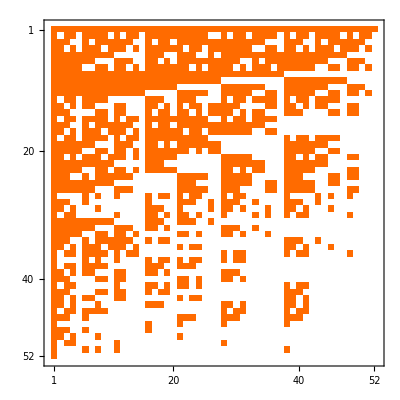

```mathematica
Inverse[conv]//MatrixPlot
```

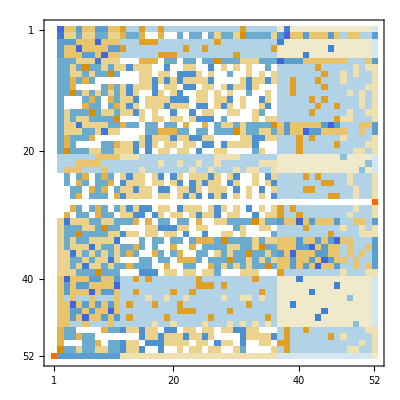

```mathematica
Sort[conv]//MatrixPlot
```

```mathematica
Table[allGraphs5[k,"colofournull"]==allGraphs5[k,"colofourrealnull"],{k,allGraphs5FakeAtomKeys}]
```

{p1x2x3x4x5==n1x2x3x4x5,p12x3x4x5==-n12x3x4x5+n1x2x3x4x5,p12345==24 n12345-6 n1234x5-6 n1235x4-2 n123x45+2 n123x4x5-6 n1245x3-2 n124x35+2 n124x3x5-2 n125x34+2 n125x3x4-2 n12x345+n12x34x5+n12x35x4+n12x3x45-n12x3x4x5-6 n1345x2-2 n134x25+2 n134x2x5-2 n135x24+2 n135x2x4-2 n13x245+n13x24x5+n13x25x4+n13x2x45-n13x2x4x5-2 n145x23+2 n145x2x3-2 n14x235+n14x23x5+n14x25x3+n14x2x35-n14x2x3x5-2 n15x234+n15x23x4+n15x24x3+n15x2x34-n15x2x3x4-6 n1x2345+2 n1x234x5+2 n1x235x4+n1x23x45-n1x23x4x5+2 n1x245x3+n1x24x35-n1x24x3x5+n1x25x34-n1x25x3x4+2 n1x2x345-n1x2x34x5-n1x2x35x4-n1x2x3x45+n1x2x3x4x5,p1234x5==-6 n1234x5+2 n123x4x5+2 n124x3x5+n12x34x5-n12x3x4x5+2 n134x2x5+n13x24x5-n13x2x4x5+n14x23x5-n14x2x3x5+2 n1x234x5-n1x23x4x5-n1x24x3x5-n1x2x34x5+n1x2x3x4x5,p1235x4==-6 n1235x4+2 n123x4x5+2 n125x3x4+n12x35x4-n12x3x4x5+2 n135x2x4+n13x25x4-n13x2x4x5+n15x23x4-n15x2x3x4+2 n1x235x4-n1x23x4x5-n1x25x3x4-n1x2x35x4+n1x2x3x4x5,p123x4x5==2 n123x4x5-n12x3x4x5-n13x2x4x5-n1x23x4x5+n1x2x3x4x5,p123x45==-2 n123x45+2 n123x4x5+n12x3x45-n12x3x4x5+n13x2x45-n13x2x4x5+n1x23x45-n1x23x4x5-n1x2x3x45+n1x2x3x4x5,p1245x3==-6 n1245x3+2 n124x3x5+2 n125x3x4+n12x3x45-n12x3x4x5+2 n145x2x3+n14x25x3-n14x2x3x5+n15x24x3-n15x2x3x4+2 n1x245x3-n1x24x3x5-n1x25x3x4-n1x2x3x45+n1x2x3x4x5,p124x3x5==2 n124x3x5-n12x3x4x5-n14x2x3x5-n1x24x3x5+n1x2x3x4x5,p124x35==-2 n124x35+2 n124x3x5+n12x35x4-n12x3x4x5+n14x2x35-n14x2x3x5+n1x24x35-n1x24x3x5-n1x2x35x4+n1x2x3x4x5,p125x3x4==2 n125x3x4-n12x3x4x5-n15x2x3x4-n1x25x3x4+n1x2x3x4x5,p125x34==-2 n125x34+2 n125x3x4+n12x34x5-n12x3x4x5+n15x2x34-n15x2x3x4+n1x25x34-n1x25x3x4-n1x2x34x5+n1x2x3x4x5,p12x34x5==n12x34x5-n12x3x4x5-n1x2x34x5+n1x2x3x4x5,p12x345==-2 n12x345+n12x34x5+n12x35x4+n12x3x45-n12x3x4x5+2 n1x2x345-n1x2x34x5-n1x2x35x4-n1x2x3x45+n1x2x3x4x5,p12x35x4==n12x35x4-n12x3x4x5-n1x2x35x4+n1x2x3x4x5,p12x3x45==n12x3x45-n12x3x4x5-n1x2x3x45+n1x2x3x4x5,p13x2x4x5==-n13x2x4x5+n1x2x3x4x5,p1345x2==-6 n1345x2+2 n134x2x5+2 n135x2x4+n13x2x45-n13x2x4x5+2 n145x2x3+n14x2x35-n14x2x3x5+n15x2x34-n15x2x3x4+2 n1x2x345-n1x2x34x5-n1x2x35x4-n1x2x3x45+n1x2x3x4x5,p134x25==-2 n134x25+2 n134x2x5+n13x25x4-n13x2x4x5+n14x25x3-n14x2x3x5+n1x25x34-n1x25x3x4-n1x2x34x5+n1x2x3x4x5,p134x2x5==2 n134x2x5-n13x2x4x5-n14x2x3x5-n1x2x34x5+n1x2x3x4x5,p135x24==-2 n135x24+2 n135x2x4+n13x24x5-n13x2x4x5+n15x24x3-n15x2x3x4+n1x24x35-n1x24x3x5-n1x2x35x4+n1x2x3x4x5,p135x2x4==2 n135x2x4-n13x2x4x5-n15x2x3x4-n1x2x35x4+n1x2x3x4x5,p13x24x5==n13x24x5-n13x2x4x5-n1x24x3x5+n1x2x3x4x5,p13x245==-2 n13x245+n13x24x5+n13x25x4+n13x2x45-n13x2x4x5+2 n1x245x3-n1x24x3x5-n1x25x3x4-n1x2x3x45+n1x2x3x4x5,p13x25x4==n13x25x4-n13x2x4x5-n1x25x3x4+n1x2x3x4x5,p13x2x45==n13x2x45-n13x2x4x5-n1x2x3x45+n1x2x3x4x5,p14x2x3x5==-n14x2x3x5+n1x2x3x4x5,p145x23==-2 n145x23+2 n145x2x3+n14x23x5-n14x2x3x5+n15x23x4-n15x2x3x4+n1x23x45-n1x23x4x5-n1x2x3x45+n1x2x3x4x5,p145x2x3==2 n145x2x3-n14x2x3x5-n15x2x3x4-n1x2x3x45+n1x2x3x4x5,p14x23x5==n14x23x5-n14x2x3x5-n1x23x4x5+n1x2x3x4x5,p14x235==-2 n14x235+n14x23x5+n14x25x3+n14x2x35-n14x2x3x5+2 n1x235x4-n1x23x4x5-n1x25x3x4-n1x2x35x4+n1x2x3x4x5,p14x25x3==n14x25x3-n14x2x3x5-n1x25x3x4+n1x2x3x4x5,p14x2x35==n14x2x35-n14x2x3x5-n1x2x35x4+n1x2x3x4x5,p15x2x3x4==-n15x2x3x4+n1x2x3x4x5,p15x23x4==n15x23x4-n15x2x3x4-n1x23x4x5+n1x2x3x4x5,p15x234==-2 n15x234+n15x23x4+n15x24x3+n15x2x34-n15x2x3x4+2 n1x234x5-n1x23x4x5-n1x24x3x5-n1x2x34x5+n1x2x3x4x5,p15x24x3==n15x24x3-n15x2x3x4-n1x24x3x5+n1x2x3x4x5,p15x2x34==n15x2x34-n15x2x3x4-n1x2x34x5+n1x2x3x4x5,p1x23x4x5==-n1x23x4x5+n1x2x3x4x5,p1x2345==-6 n1x2345+2 n1x234x5+2 n1x235x4+n1x23x45-n1x23x4x5+2 n1x245x3+n1x24x35-n1x24x3x5+n1x25x34-n1x25x3x4+2 n1x2x345-n1x2x34x5-n1x2x35x4-n1x2x3x45+n1x2x3x4x5,p1x234x5==2 n1x234x5-n1x23x4x5-n1x24x3x5-n1x2x34x5+n1x2x3x4x5,p1x235x4==2 n1x235x4-n1x23x4x5-n1x25x3x4-n1x2x35x4+n1x2x3x4x5,p1x23x45==n1x23x45-n1x23x4x5-n1x2x3x45+n1x2x3x4x5,p1x24x3x5==-n1x24x3x5+n1x2x3x4x5,p1x245x3==2 n1x245x3-n1x24x3x5-n1x25x3x4-n1x2x3x45+n1x2x3x4x5,p1x24x35==n1x24x35-n1x24x3x5-n1x2x35x4+n1x2x3x4x5,p1x25x3x4==-n1x25x3x4+n1x2x3x4x5,p1x25x34==n1x25x34-n1x25x3x4-n1x2x34x5+n1x2x3x4x5,p1x2x34x5==-n1x2x34x5+n1x2x3x4x5,p1x2x345==2 n1x2x345-n1x2x34x5-n1x2x35x4-n1x2x3x45+n1x2x3x4x5,p1x2x35x4==-n1x2x35x4+n1x2x3x4x5,p1x2x3x45==-n1x2x3x45+n1x2x3x4x5}

```mathematica
sols2=Sort[Solve[Table[allGraphs5[k,"colofournull"]==allGraphs5[k,"colofourrealnull"],{k,allGraphs5FakeAtomKeys}],Table[allGraphs5[k,"colofourrealnull"],{k,allGraphs5NullAtomKeys}]],CompareSymbols[#1[[1]],#2[[1]] ]&]
```

{{n1x2x3x4x5→p1x2x3x4x5,n12x3x4x5→-p12x3x4x5+p1x2x3x4x5,n123x4x5→1/2 (p123x4x5-p12x3x4x5-p13x2x4x5-p1x23x4x5+2 p1x2x3x4x5),n1234x5→1/6 (-p1234x5+p123x4x5+p124x3x5+p12x34x5-2 p12x3x4x5+p134x2x5+p13x24x5-2 p13x2x4x5+p14x23x5-2 p14x2x3x5+p1x234x5-2 p1x23x4x5-2 p1x24x3x5-2 p1x2x34x5+6 p1x2x3x4x5),n12345→1/24 (p12345-p1234x5-p1235x4-p123x45+2 p123x4x5-p1245x3-p124x35+2 p124x3x5-p125x34+2 p125x3x4-p12x345+2 p12x34x5+2 p12x35x4+2 p12x3x45-6 p12x3x4x5-p1345x2-p134x25+2 p134x2x5-p135x24+2 p135x2x4-p13x245+2 p13x24x5+2 p13x25x4+2 p13x2x45-6 p13x2x4x5-p145x23+2 p145x2x3-p14x235+2 p14x23x5+2 p14x25x3+2 p14x2x35-6 p14x2x3x5-p15x234+2 p15x23x4+2 p15x24x3+2 p15x2x34-6 p15x2x3x4-p1x2345+2 p1x234x5+2 p1x235x4+2 p1x23x45-6 p1x23x4x5+2 p1x245x3+2 p1x24x35-6 p1x24x3x5+2 p1x25x34-6 p1x25x3x4+2 p1x2x345-6 p1x2x34x5-6 p1x2x35x4-6 p1x2x3x45+24 p1x2x3x4x5),n1235x4→1/6 (-p1235x4+p123x4x5+p125x3x4+p12x35x4-2 p12x3x4x5+p135x2x4+p13x25x4-2 p13x2x4x5+p15x23x4-2 p15x2x3x4+p1x235x4-2 p1x23x4x5-2 p1x25x3x4-2 p1x2x35x4+6 p1x2x3x4x5),n123x45→1/2 (-p123x45+p123x4x5+p12x3x45-p12x3x4x5+p13x2x45-p13x2x4x5+p1x23x45-p1x23x4x5-2 p1x2x3x45+2 p1x2x3x4x5),n124x3x5→1/2 (p124x3x5-p12x3x4x5-p14x2x3x5-p1x24x3x5+2 p1x2x3x4x5),n1245x3→1/6 (-p1245x3+p124x3x5+p125x3x4+p12x3x45-2 p12x3x4x5+p145x2x3+p14x25x3-2 p14x2x3x5+p15x24x3-2 p15x2x3x4+p1x245x3-2 p1x24x3x5-2 p1x25x3x4-2 p1x2x3x45+6 p1x2x3x4x5),n124x35→1/2 (-p124x35+p124x3x5+p12x35x4-p12x3x4x5+p14x2x35-p14x2x3x5+p1x24x35-p1x24x3x5-2 p1x2x35x4+2 p1x2x3x4x5),n125x3x4→1/2 (p125x3x4-p12x3x4x5-p15x2x3x4-p1x25x3x4+2 p1x2x3x4x5),n125x34→1/2 (-p125x34+p125x3x4+p12x34x5-p12x3x4x5+p15x2x34-p15x2x3x4+p1x25x34-p1x25x3x4-2 p1x2x34x5+2 p1x2x3x4x5),n12x34x5→p12x34x5-p12x3x4x5-p1x2x34x5+p1x2x3x4x5,n12x345→1/2 (-p12x345+p12x34x5+p12x35x4+p12x3x45-2 p12x3x4x5+p1x2x345-p1x2x34x5-p1x2x35x4-p1x2x3x45+2 p1x2x3x4x5),n12x35x4→p12x35x4-p12x3x4x5-p1x2x35x4+p1x2x3x4x5,n12x3x45→p12x3x45-p12x3x4x5-p1x2x3x45+p1x2x3x4x5,n13x2x4x5→-p13x2x4x5+p1x2x3x4x5,n134x2x5→1/2 (p134x2x5-p13x2x4x5-p14x2x3x5-p1x2x34x5+2 p1x2x3x4x5),n1345x2→1/6 (-p1345x2+p134x2x5+p135x2x4+p13x2x45-2 p13x2x4x5+p145x2x3+p14x2x35-2 p14x2x3x5+p15x2x34-2 p15x2x3x4+p1x2x345-2 p1x2x34x5-2 p1x2x35x4-2 p1x2x3x45+6 p1x2x3x4x5),n134x25→1/2 (-p134x25+p134x2x5+p13x25x4-p13x2x4x5+p14x25x3-p14x2x3x5+p1x25x34-2 p1x25x3x4-p1x2x34x5+2 p1x2x3x4x5),n135x2x4→1/2 (p135x2x4-p13x2x4x5-p15x2x3x4-p1x2x35x4+2 p1x2x3x4x5),n135x24→1/2 (-p135x24+p135x2x4+p13x24x5-p13x2x4x5+p15x24x3-p15x2x3x4+p1x24x35-2 p1x24x3x5-p1x2x35x4+2 p1x2x3x4x5),n13x24x5→p13x24x5-p13x2x4x5-p1x24x3x5+p1x2x3x4x5,n13x245→1/2 (-p13x245+p13x24x5+p13x25x4+p13x2x45-2 p13x2x4x5+p1x245x3-p1x24x3x5-p1x25x3x4-p1x2x3x45+2 p1x2x3x4x5),n13x25x4→p13x25x4-p13x2x4x5-p1x25x3x4+p1x2x3x4x5,n13x2x45→p13x2x45-p13x2x4x5-p1x2x3x45+p1x2x3x4x5,n14x2x3x5→-p14x2x3x5+p1x2x3x4x5,n145x2x3→1/2 (p145x2x3-p14x2x3x5-p15x2x3x4-p1x2x3x45+2 p1x2x3x4x5),n145x23→1/2 (-p145x23+p145x2x3+p14x23x5-p14x2x3x5+p15x23x4-p15x2x3x4+p1x23x45-2 p1x23x4x5-p1x2x3x45+2 p1x2x3x4x5),n14x23x5→p14x23x5-p14x2x3x5-p1x23x4x5+p1x2x3x4x5,n14x235→1/2 (-p14x235+p14x23x5+p14x25x3+p14x2x35-2 p14x2x3x5+p1x235x4-p1x23x4x5-p1x25x3x4-p1x2x35x4+2 p1x2x3x4x5),n14x25x3→p14x25x3-p14x2x3x5-p1x25x3x4+p1x2x3x4x5,n14x2x35→p14x2x35-p14x2x3x5-p1x2x35x4+p1x2x3x4x5,n15x2x3x4→-p15x2x3x4+p1x2x3x4x5,n15x23x4→p15x23x4-p15x2x3x4-p1x23x4x5+p1x2x3x4x5,n15x234→1/2 (-p15x234+p15x23x4+p15x24x3+p15x2x34-2 p15x2x3x4+p1x234x5-p1x23x4x5-p1x24x3x5-p1x2x34x5+2 p1x2x3x4x5),n15x24x3→p15x24x3-p15x2x3x4-p1x24x3x5+p1x2x3x4x5,n15x2x34→p15x2x34-p15x2x3x4-p1x2x34x5+p1x2x3x4x5,n1x23x4x5→-p1x23x4x5+p1x2x3x4x5,n1x234x5→1/2 (p1x234x5-p1x23x4x5-p1x24x3x5-p1x2x34x5+2 p1x2x3x4x5),n1x2345→1/6 (-p1x2345+p1x234x5+p1x235x4+p1x23x45-2 p1x23x4x5+p1x245x3+p1x24x35-2 p1x24x3x5+p1x25x34-2 p1x25x3x4+p1x2x345-2 p1x2x34x5-2 p1x2x35x4-2 p1x2x3x45+6 p1x2x3x4x5),n1x235x4→1/2 (p1x235x4-p1x23x4x5-p1x25x3x4-p1x2x35x4+2 p1x2x3x4x5),n1x23x45→p1x23x45-p1x23x4x5-p1x2x3x45+p1x2x3x4x5,n1x24x3x5→-p1x24x3x5+p1x2x3x4x5,n1x245x3→1/2 (p1x245x3-p1x24x3x5-p1x25x3x4-p1x2x3x45+2 p1x2x3x4x5),n1x24x35→p1x24x35-p1x24x3x5-p1x2x35x4+p1x2x3x4x5,n1x25x3x4→-p1x25x3x4+p1x2x3x4x5,n1x25x34→p1x25x34-p1x25x3x4-p1x2x34x5+p1x2x3x4x5,n1x2x34x5→-p1x2x34x5+p1x2x3x4x5,n1x2x345→1/2 (p1x2x345-p1x2x34x5-p1x2x35x4-p1x2x3x45+2 p1x2x3x4x5),n1x2x35x4→-p1x2x35x4+p1x2x3x4x5,n1x2x3x45→-p1x2x3x45+p1x2x3x4x5}}

```mathematica
fakeCoeff[exp_]:=Table[Coefficient[exp,k],{k,fakeAtoms}]
```

```mathematica
conv2=Map[fakeCoeff[#[[2]]]&,sols2[[1]]];MatrixForm[conv]
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | -1/2 | 1/6 | 1/6 | -1/6 | 1/6 | 1/6 | -1/6 | -1/6 | 1/6 | 1/6 | 1/3 | -1/6 | -1/6 | 1/3 | 0 | 0 | 1/3 | 0 | 0 | -1/6 | 0 | -1/6 | -1/6 | 0 | -1/6 | 1/6 | -1/6 | -1/6 | 1/6 | 1/2 | -1/6 | -1/6 | -1/6 | -1/6 | 1/6 | -1/4 | -3/4 | 1/4 | 1/4 | -1/4 | 1/4 | 1/4 | 1/4 | -1/4 | 1/4 | -1/12 | 1/4 | 1/4 | -1/12 | -1/12 | -1/4
0 | 1/6 | 1/6 | -1/2 | 1/6 | -1/6 | 1/6 | -1/6 | 1/6 | -1/6 | 1/6 | -1/6 | 1/3 | -1/6 | 0 | 0 | 1/3 | -1/6 | 0 | -1/6 | 1/3 | 0 | 0 | -1/6 | -1/6 | 0 | 1/6 | -1/6 | 1/6 | -1/6 | -1/6 | 1/2 | -1/6 | -1/6 | 1/6 | -1/6 | -1/4 | 1/4 | -3/4 | 1/4 | 1/4 | 1/4 | -1/4 | -1/4 | 1/4 | 1/4 | -1/12 | 1/4 | -1/12 | 1/4 | -1/12 | -1/4
0 | 1/6 | -1/2 | 1/6 | 1/6 | 1/6 | -1/6 | -1/6 | 1/6 | 1/6 | -1/6 | -1/6 | -1/6 | 1/3 | 0 | 1/3 | 0 | -1/6 | -1/6 | 0 | -1/6 | -1/6 | 0 | 1/3 | 0 | 0 | 1/6 | 1/6 | -1/6 | -1/6 | -1/6 | -1/6 | 1/2 | 1/6 | -1/6 | -1/6 | -1/4 | 1/4 | 1/4 | -3/4 | 1/4 | -1/4 | 1/4 | 1/4 | 1/4 | -1/4 | -1/12 | -1/12 | 1/4 | 1/4 | -1/12 | -1/4
0 | 1/6 | 1/6 | 1/6 | -1/6 | -1/6 | -1/6 | 1/2 | -1/6 | -1/6 | -1/6 | 0 | 0 | 0 | -1/3 | -1/3 | -1/3 | 0 | 1/6 | 1/6 | 0 | 1/6 | 1/6 | 0 | 1/6 | 1/6 | -1/6 | 0 | 0 | 0 | 1/6 | 1/6 | 1/6 | 0 | 0 | 0 | 5/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 1/12 | -1/12 | -1/12 | -1/12 | 1/12 | 1/12
0 | 1/6 | -1/6 | 1/6 | 1/6 | 1/6 | -1/2 | 1/6 | -1/6 | -1/6 | 1/6 | -1/6 | -1/6 | 1/3 | -1/6 | 0 | -1/6 | 0 | 0 | 1/3 | 0 | 0 | 1/3 | 0 | -1/6 | -1/6 | -1/6 | -1/6 | 1/6 | 1/6 | -1/6 | -1/6 | 1/6 | 1/2 | -1/6 | -1/6 | 1/4 | 1/4 | 1/4 | -1/4 | -1/4 | -3/4 | 1/4 | -1/4 | 1/4 | 1/4 | -1/12 | 1/4 | -1/12 | -1/12 | 1/4 | -1/4
0 | -1/6 | 1/3 | -1/6 | -1/6 | -1/6 | 1/3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/6 | -1/3 | 1/6 | 1/6 | 1/6 | -1/3 | 1/6 | 1/6 | -1/3 | -1/3 | 1/6 | 1/6 | 0 | 0 | 0 | 0 | 1/6 | 1/6 | -1/3 | -1/3 | 1/6 | 1/6 | -1/12 | -1/12 | -1/12 | 5/12 | -1/12 | 5/12 | -1/12 | -1/12 | -1/12 | -1/12 | 1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 1/12
0 | 1/6 | 1/6 | -1/6 | 1/6 | -1/2 | 1/6 | 1/6 | -1/6 | 1/6 | -1/6 | -1/6 | 1/3 | -1/6 | -1/6 | -1/6 | 0 | 0 | 1/3 | 0 | 0 | -1/6 | -1/6 | 0 | 0 | 1/3 | -1/6 | 1/6 | -1/6 | 1/6 | -1/6 | 1/6 | -1/6 | -1/6 | 1/2 | -1/6 | 1/4 | 1/4 | -1/4 | 1/4 | -1/4 | 1/4 | -3/4 | 1/4 | 1/4 | -1/4 | -1/12 | -1/12 | 1/4 | -1/12 | 1/4 | -1/4
0 | -1/6 | -1/6 | 1/3 | -1/6 | 1/3 | -1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/6 | 1/6 | -1/3 | 1/6 | -1/3 | 1/6 | -1/3 | 1/6 | 1/6 | 1/6 | 1/6 | -1/3 | 0 | 0 | 0 | 0 | 1/6 | -1/3 | 1/6 | 1/6 | -1/3 | 1/6 | -1/12 | -1/12 | 5/12 | -1/12 | -1/12 | -1/12 | 5/12 | -1/12 | -1/12 | -1/12 | 1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 1/12
0 | 1/6 | -1/6 | -1/6 | -1/6 | 1/6 | 1/6 | -1/6 | 1/2 | -1/6 | -1/6 | 0 | 0 | 0 | 0 | 1/6 | 1/6 | -1/3 | -1/3 | -1/3 | 1/6 | 1/6 | 0 | 1/6 | 1/6 | 0 | 0 | 0 | 0 | -1/6 | 1/6 | 0 | 0 | 1/6 | 1/6 | 0 | -1/12 | -1/12 | -1/12 | -1/12 | 5/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 1/12 | -1/12 | -1/12 | 1/12 | -1/12 | 1/12
0 | -1/6 | 1/6 | 1/6 | -1/2 | 1/6 | 1/6 | 1/6 | 1/6 | -1/6 | -1/6 | 1/3 | -1/6 | -1/6 | 0 | -1/6 | -1/6 | 0 | -1/6 | -1/6 | 0 | 1/3 | 0 | 0 | 1/3 | 0 | -1/6 | 1/6 | 1/6 | -1/6 | 1/6 | -1/6 | -1/6 | -1/6 | -1/6 | 1/2 | 1/4 | -1/4 | 1/4 | 1/4 | 1/4 | 1/4 | 1/4 | -1/4 | -3/4 | -1/4 | -1/12 | -1/12 | -1/12 | 1/4 | 1/4 | -1/4
0 | 1/3 | -1/6 | -1/6 | 1/3 | -1/6 | -1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/3 | 1/6 | 1/6 | -1/3 | 1/6 | 1/6 | 1/6 | -1/3 | 1/6 | 1/6 | -1/3 | 1/6 | 0 | 0 | 0 | 0 | -1/3 | 1/6 | 1/6 | 1/6 | 1/6 | -1/3 | -1/12 | 5/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 5/12 | -1/12 | 1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 1/12
0 | -1/6 | -1/6 | 1/6 | 1/6 | -1/6 | 1/6 | -1/6 | -1/6 | 1/2 | -1/6 | 0 | 0 | 0 | 1/6 | 1/6 | 0 | 1/6 | 1/6 | 0 | -1/3 | -1/3 | -1/3 | 1/6 | 0 | 1/6 | 0 | 0 | -1/6 | 0 | 0 | 1/6 | 0 | 1/6 | 0 | 1/6 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 5/12 | -1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | -1/12 | 1/12
0 | -1/6 | 1/6 | -1/6 | 1/6 | 1/6 | -1/6 | -1/6 | -1/6 | -1/6 | 1/2 | 0 | 0 | 0 | 1/6 | 0 | 1/6 | 1/6 | 0 | 1/6 | 1/6 | 0 | 1/6 | -1/3 | -1/3 | -1/3 | 0 | -1/6 | 0 | 0 | 0 | 0 | 1/6 | 0 | 1/6 | 1/6 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 5/12 | 1/12 | 1/12 | -1/12 | -1/12 | -1/12 | 1/12
0 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 1/4 | 1/4 | 1/4 | 1/4 | 1/12 | 1/12 | 1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 1/12 | 1/12 | 1/12 | 1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | -1/8 | 1/24 | 1/24 | 1/24 | 1/24 | -1/24
0 | 1/6 | -1/6 | 1/6 | -1/6 | -1/6 | 1/6 | 1/6 | 1/6 | 1/6 | -1/2 | 0 | 0 | 0 | -1/6 | 0 | -1/6 | -1/6 | 0 | -1/6 | -1/6 | 0 | -1/6 | 1/3 | 1/3 | 1/3 | -1/6 | 1/2 | -1/6 | -1/6 | -1/6 | -1/6 | 1/6 | -1/6 | 1/6 | 1/6 | 1/4 | 1/4 | 1/4 | -1/4 | 1/4 | 1/4 | -1/4 | 1/4 | -1/4 | -3/4 | 1/4 | 1/4 | -1/12 | -1/12 | -1/12 | -1/4
0 | -1/6 | 1/3 | -1/6 | 0 | 0 | 0 | 0 | -1/6 | -1/6 | 1/3 | 1/6 | 1/6 | -1/3 | 1/6 | -1/3 | 1/6 | 0 | 1/6 | 1/6 | 0 | 1/6 | 1/6 | 0 | -1/3 | -1/3 | 0 | -1/3 | 1/6 | 1/6 | 1/6 | 1/6 | -1/3 | 0 | 0 | 0 | -1/12 | -1/12 | -1/12 | 5/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 5/12 | -1/12 | -1/12 | -1/12 | -1/12 | 1/12 | 1/12
0 | -1/6 | 0 | 0 | 0 | 1/3 | -1/6 | -1/6 | 0 | -1/6 | 1/3 | 1/6 | -1/3 | 1/6 | 0 | 1/6 | 1/6 | 1/6 | -1/3 | 1/6 | 1/6 | 1/6 | 0 | -1/3 | -1/3 | 0 | 1/6 | -1/3 | 1/6 | 0 | 1/6 | 0 | 0 | 1/6 | -1/3 | 0 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 5/12 | -1/12 | -1/12 | 5/12 | -1/12 | -1/12 | -1/12 | 1/12 | -1/12 | 1/12
0 | 0 | 0 | -1/6 | 1/3 | 0 | -1/6 | -1/6 | -1/6 | 0 | 1/3 | -1/3 | 1/6 | 1/6 | 1/6 | 1/6 | 0 | 1/6 | 1/6 | 0 | 1/6 | -1/3 | 1/6 | -1/3 | 0 | -1/3 | 1/6 | -1/3 | 0 | 1/6 | 0 | 1/6 | 0 | 1/6 | 0 | -1/3 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 5/12 | 5/12 | -1/12 | -1/12 | 1/12 | -1/12 | -1/12 | 1/12
0 | 1/4 | -1/4 | 1/4 | -1/4 | -1/4 | 1/4 | 1/4 | 1/4 | 1/4 | -3/4 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 5/12 | 5/12 | 5/12 | -1/12 | 5/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | -11/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | -1/24
0 | 1/6 | 1/6 | -1/6 | -1/6 | 1/6 | -1/6 | 1/6 | 1/6 | -1/2 | 1/6 | 0 | 0 | 0 | -1/6 | -1/6 | 0 | -1/6 | -1/6 | 0 | 1/3 | 1/3 | 1/3 | -1/6 | 0 | -1/6 | -1/6 | -1/6 | 1/2 | -1/6 | -1/6 | 1/6 | -1/6 | 1/6 | -1/6 | 1/6 | 1/4 | 1/4 | -1/4 | 1/4 | 1/4 | -1/4 | 1/4 | -3/4 | -1/4 | 1/4 | 1/4 | -1/12 | 1/4 | -1/12 | -1/12 | -1/4
0 | -1/6 | -1/6 | 1/3 | 0 | 0 | 0 | 0 | -1/6 | 1/3 | -1/6 | 1/6 | -1/3 | 1/6 | 1/6 | 1/6 | -1/3 | 0 | 1/6 | 1/6 | 0 | -1/3 | -1/3 | 0 | 1/6 | 1/6 | 0 | 1/6 | -1/3 | 1/6 | 1/6 | -1/3 | 1/6 | 0 | 0 | 0 | -1/12 | -1/12 | 5/12 | -1/12 | -1/12 | -1/12 | -1/12 | 5/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 1/12 | 1/12
0 | -1/6 | 0 | 0 | 0 | -1/6 | 1/3 | -1/6 | 0 | 1/3 | -1/6 | 1/6 | 1/6 | -1/3 | 0 | 1/6 | 1/6 | 1/6 | 1/6 | -1/3 | -1/3 | -1/3 | 0 | 1/6 | 1/6 | 0 | 1/6 | 1/6 | -1/3 | 0 | 1/6 | 0 | 0 | -1/3 | 1/6 | 0 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 5/12 | -1/12 | 5/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 1/12 | -1/12 | 1/12
0 | 0 | -1/6 | 0 | 1/3 | -1/6 | 0 | -1/6 | -1/6 | 1/3 | 0 | -1/3 | 1/6 | 1/6 | 1/6 | 0 | 1/6 | 1/6 | 0 | 1/6 | -1/3 | 0 | -1/3 | 1/6 | -1/3 | 1/6 | 1/6 | 0 | -1/3 | 1/6 | 0 | 0 | 1/6 | 0 | 1/6 | -1/3 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 5/12 | 5/12 | -1/12 | -1/12 | 1/12 | -1/12 | -1/12 | -1/12 | 1/12
0 | 1/4 | 1/4 | -1/4 | -1/4 | 1/4 | -1/4 | 1/4 | 1/4 | -3/4 | 1/4 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 5/12 | 5/12 | 5/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 5/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | -11/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | -1/24
0 | 1/6 | -1/6 | -1/6 | 1/2 | -1/6 | -1/6 | -1/6 | -1/6 | 1/6 | 1/6 | -1/3 | 1/6 | 1/6 | 0 | 1/6 | 1/6 | 0 | 1/6 | 1/6 | 0 | -1/3 | 0 | 0 | -1/3 | 0 | 0 | 1/6 | 1/6 | 0 | 1/6 | 0 | 0 | 0 | 0 | -1/6 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 5/12 | -1/12 | -1/12 | -1/12 | -1/12 | 1/12 | 1/12 | 1/12
0 | -1/4 | 1/4 | 1/4 | -3/4 | 1/4 | 1/4 | 1/4 | 1/4 | -1/4 | -1/4 | 5/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 5/12 | -1/12 | -1/12 | 5/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 5/12 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | -11/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | -1/24
0 | -1/6 | 1/6 | 1/6 | 1/6 | -1/6 | -1/6 | 1/6 | -1/2 | 1/6 | 1/6 | 0 | 0 | 0 | 0 | -1/6 | -1/6 | 1/3 | 1/3 | 1/3 | -1/6 | -1/6 | 0 | -1/6 | -1/6 | 0 | -1/6 | -1/6 | -1/6 | 1/2 | 1/6 | -1/6 | -1/6 | 1/6 | 1/6 | -1/6 | 1/4 | -1/4 | 1/4 | 1/4 | -3/4 | -1/4 | -1/4 | 1/4 | 1/4 | 1/4 | 1/4 | -1/12 | -1/12 | 1/4 | -1/12 | -1/4
0 | 1/3 | -1/6 | -1/6 | 0 | 0 | 0 | 0 | 1/3 | -1/6 | -1/6 | -1/3 | 1/6 | 1/6 | -1/3 | 1/6 | 1/6 | 0 | -1/3 | -1/3 | 0 | 1/6 | 1/6 | 0 | 1/6 | 1/6 | 0 | 1/6 | 1/6 | -1/3 | -1/3 | 1/6 | 1/6 | 0 | 0 | 0 | -1/12 | 5/12 | -1/12 | -1/12 | 5/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 1/12 | 1/12
0 | 0 | 0 | -1/6 | -1/6 | 0 | 1/3 | -1/6 | 1/3 | 0 | -1/6 | 1/6 | 1/6 | -1/3 | 1/6 | 1/6 | 0 | -1/3 | -1/3 | 0 | 1/6 | 1/6 | -1/3 | 1/6 | 0 | 1/6 | 1/6 | 1/6 | 0 | -1/3 | 0 | 1/6 | 0 | -1/3 | 0 | 1/6 | -1/12 | -1/12 | -1/12 | -1/12 | 5/12 | 5/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 1/12 | -1/12 | -1/12 | 1/12
0 | 0 | -1/6 | 0 | -1/6 | 1/3 | 0 | -1/6 | 1/3 | -1/6 | 0 | 1/6 | -1/3 | 1/6 | 1/6 | 0 | 1/6 | -1/3 | 0 | -1/3 | 1/6 | 0 | 1/6 | 1/6 | 1/6 | -1/3 | 1/6 | 0 | 1/6 | -1/3 | 0 | 0 | 1/6 | 0 | -1/3 | 1/6 | -1/12 | -1/12 | -1/12 | -1/12 | 5/12 | -1/12 | 5/12 | -1/12 | -1/12 | -1/12 | -1/12 | 1/12 | -1/12 | -1/12 | -1/12 | 1/12
0 | -1/4 | 1/4 | 1/4 | 1/4 | -1/4 | -1/4 | 1/4 | -3/4 | 1/4 | 1/4 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 5/12 | 5/12 | 5/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 5/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 1/24 | 1/24 | 1/24 | 1/24 | -11/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | -1/24
0 | -1/6 | -1/6 | 1/6 | -1/6 | 1/2 | -1/6 | -1/6 | 1/6 | -1/6 | 1/6 | 1/6 | -1/3 | 1/6 | 1/6 | 1/6 | 0 | 0 | -1/3 | 0 | 0 | 1/6 | 1/6 | 0 | 0 | -1/3 | 0 | 1/6 | 0 | 1/6 | 0 | 1/6 | 0 | 0 | -1/6 | 0 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 5/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 1/12 | -1/12 | 1/12 | 1/12
0 | 1/4 | 1/4 | -1/4 | 1/4 | -3/4 | 1/4 | 1/4 | -1/4 | 1/4 | -1/4 | -1/12 | 5/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 5/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 5/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 5/12 | -1/12 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | -11/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | -1/24
0 | -1/6 | 1/6 | -1/6 | -1/6 | -1/6 | 1/2 | -1/6 | 1/6 | 1/6 | -1/6 | 1/6 | 1/6 | -1/3 | 1/6 | 0 | 1/6 | 0 | 0 | -1/3 | 0 | 0 | -1/3 | 0 | 1/6 | 1/6 | 0 | 0 | 1/6 | 1/6 | 0 | 0 | 1/6 | -1/6 | 0 | 0 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 5/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 1/12 | -1/12 | -1/12 | 1/12 | 1/12
0 | 1/4 | -1/4 | 1/4 | 1/4 | 1/4 | -3/4 | 1/4 | -1/4 | -1/4 | 1/4 | -1/12 | -1/12 | 5/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 5/12 | -1/12 | -1/12 | 5/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 5/12 | -1/12 | -1/12 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | -11/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | -1/24
0 | -1/12 | -1/12 | -1/12 | 1/4 | 1/4 | 1/4 | 1/4 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 1/12 | -1/12 | -1/12 | 1/12 | -1/12 | -1/12 | 1/12 | -1/12 | -1/12 | 1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 1/12 | 1/12 | 1/12 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | -1/8 | -1/24
0 | -1/6 | -1/6 | -1/6 | 1/6 | 1/6 | 1/6 | -1/2 | 1/6 | 1/6 | 1/6 | 0 | 0 | 0 | 1/3 | 1/3 | 1/3 | 0 | -1/6 | -1/6 | 0 | -1/6 | -1/6 | 0 | -1/6 | -1/6 | 1/2 | -1/6 | -1/6 | -1/6 | 1/6 | 1/6 | 1/6 | -1/6 | -1/6 | -1/6 | -3/4 | -1/4 | -1/4 | -1/4 | 1/4 | 1/4 | 1/4 | 1/4 | 1/4 | 1/4 | 1/4 | -1/12 | -1/12 | -1/12 | 1/4 | -1/4
0 | 1/3 | 0 | 0 | 0 | -1/6 | -1/6 | 1/3 | 0 | -1/6 | -1/6 | -1/3 | 1/6 | 1/6 | 0 | -1/3 | -1/3 | -1/3 | 1/6 | 1/6 | 1/6 | 1/6 | 0 | 1/6 | 1/6 | 0 | -1/3 | 1/6 | 1/6 | 0 | -1/3 | 0 | 0 | 1/6 | 1/6 | 0 | 5/12 | 5/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 1/12 | -1/12 | 1/12
0 | 0 | 0 | 1/3 | -1/6 | 0 | -1/6 | 1/3 | -1/6 | 0 | -1/6 | 1/6 | -1/3 | 1/6 | -1/3 | -1/3 | 0 | 1/6 | 1/6 | 0 | -1/3 | 1/6 | 1/6 | 1/6 | 0 | 1/6 | -1/3 | 1/6 | 0 | 1/6 | 0 | -1/3 | 0 | 1/6 | 0 | 1/6 | 5/12 | -1/12 | 5/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 1/12 | -1/12 | -1/12 | 1/12
0 | 0 | 1/3 | 0 | -1/6 | -1/6 | 0 | 1/3 | -1/6 | -1/6 | 0 | 1/6 | 1/6 | -1/3 | -1/3 | 0 | -1/3 | 1/6 | 0 | 1/6 | 1/6 | 0 | 1/6 | -1/3 | 1/6 | 1/6 | -1/3 | 0 | 1/6 | 1/6 | 0 | 0 | -1/3 | 0 | 1/6 | 1/6 | 5/12 | -1/12 | -1/12 | 5/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 1/12 | -1/12 | -1/12 | -1/12 | 1/12
0 | -1/4 | -1/4 | -1/4 | 1/4 | 1/4 | 1/4 | -3/4 | 1/4 | 1/4 | 1/4 | -1/12 | -1/12 | -1/12 | 5/12 | 5/12 | 5/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 5/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -11/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | -1/24
0 | -1/6 | 1/2 | -1/6 | -1/6 | -1/6 | 1/6 | 1/6 | -1/6 | -1/6 | 1/6 | 1/6 | 1/6 | -1/3 | 0 | -1/3 | 0 | 1/6 | 1/6 | 0 | 1/6 | 1/6 | 0 | -1/3 | 0 | 0 | 1/6 | 1/6 | 0 | 0 | 0 | 0 | -1/6 | 1/6 | 0 | 0 | -1/12 | -1/12 | -1/12 | 5/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 1/12 | 1/12 | -1/12 | 1/12
0 | 1/4 | -3/4 | 1/4 | 1/4 | 1/4 | -1/4 | -1/4 | 1/4 | 1/4 | -1/4 | -1/12 | -1/12 | 5/12 | -1/12 | 5/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 5/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 5/12 | -1/12 | -1/12 | -1/12 | 1/24 | 1/24 | 1/24 | -11/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | -1/24
0 | -1/6 | -1/6 | 1/2 | -1/6 | 1/6 | -1/6 | 1/6 | -1/6 | 1/6 | -1/6 | 1/6 | -1/3 | 1/6 | 0 | 0 | -1/3 | 1/6 | 0 | 1/6 | -1/3 | 0 | 0 | 1/6 | 1/6 | 0 | 1/6 | 0 | 1/6 | 0 | 0 | -1/6 | 0 | 0 | 1/6 | 0 | -1/12 | -1/12 | 5/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12
0 | 1/4 | 1/4 | -3/4 | 1/4 | -1/4 | 1/4 | -1/4 | 1/4 | -1/4 | 1/4 | -1/12 | 5/12 | -1/12 | -1/12 | -1/12 | 5/12 | -1/12 | -1/12 | -1/12 | 5/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 5/12 | -1/12 | -1/12 | -1/12 | -1/12 | 1/24 | 1/24 | -11/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | -1/24
0 | -1/12 | 1/4 | 1/4 | 1/4 | -1/12 | -1/12 | -1/12 | 1/4 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 1/12 | -1/12 | -1/12 | 1/12 | -1/12 | -1/12 | -1/12 | 1/12 | -1/12 | 1/12 | 1/12 | -1/12 | -1/12 | 1/12 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | -1/8 | 1/24 | -1/24
0 | 1/2 | -1/6 | -1/6 | 1/6 | -1/6 | -1/6 | 1/6 | 1/6 | -1/6 | -1/6 | -1/3 | 1/6 | 1/6 | -1/3 | 0 | 0 | -1/3 | 0 | 0 | 1/6 | 0 | 1/6 | 1/6 | 0 | 1/6 | 1/6 | 0 | 0 | 1/6 | -1/6 | 0 | 0 | 0 | 0 | 1/6 | -1/12 | 5/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 1/12 | 1/12 | -1/12 | -1/12 | 1/12
0 | -3/4 | 1/4 | 1/4 | -1/4 | 1/4 | 1/4 | -1/4 | -1/4 | 1/4 | 1/4 | 5/12 | -1/12 | -1/12 | 5/12 | -1/12 | -1/12 | 5/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 5/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 1/24 | -11/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | -1/24
0 | 1/4 | 1/4 | -1/12 | -1/12 | 1/4 | -1/12 | -1/12 | -1/12 | 1/4 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 1/12 | -1/12 | -1/12 | 1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 1/12 | -1/12 | -1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | -1/8 | 1/24 | 1/24 | -1/24
0 | 1/4 | -1/12 | 1/4 | -1/12 | -1/12 | 1/4 | -1/12 | -1/12 | -1/12 | 1/4 | -1/12 | -1/12 | -1/12 | -1/12 | 1/12 | -1/12 | -1/12 | 1/12 | -1/12 | -1/12 | 1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 1/12 | -1/12 | -1/12 | 1/12 | 1/12 | -1/12 | 1/12 | -1/12 | -1/12 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | -1/8 | 1/24 | 1/24 | 1/24 | -1/24
1 | -1/4 | -1/4 | -1/4 | -1/4 | -1/4 | -1/4 | -1/4 | -1/4 | -1/4 | -1/4 | 1/12 | 1/12 | 1/12 | 1/12 | 1/12 | 1/12 | 1/12 | 1/12 | 1/12 | 1/12 | 1/12 | 1/12 | 1/12 | 1/12 | 1/12 | 1/12 | 1/12 | 1/12 | 1/12 | 1/12 | 1/12 | 1/12 | 1/12 | 1/12 | 1/12 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | 1/24)

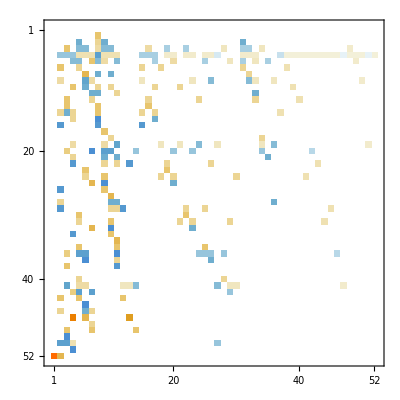

```mathematica
(conv*conv2)//MatrixPlot
```

```mathematica
Inverse[conv2]
```

{{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0},{1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,1,0,0,0,0,0,0,0,0,-1},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,1,0,0,0,0,-1,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,1,-1,0,0,0},{1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1},{1,-1,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0},{1,-1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,1,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,-1,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,1,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,1,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,2,-1,-1},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,2,0,0,0,-1,0,0,0,0,-1,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,2,0,0,0,0,-1,0,0,0,-1,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,2,0,-1,0,0,0,0,-1},{1,-1,2,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,-1,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0},{1,-1,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,2,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,2,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1},{1,-1,0,0,0,0,0,0,0,0,0,0,1,-2,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,2,-1,-1},{1,-1,2,0,0,0,-2,0,0,0,0,0,0,0,0,1,-1,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,1,0,0,0,0,0,0,0,0,-1},{1,-1,0,0,0,0,0,2,0,-2,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,-1,0,1,0,0,0,0,-1,0},{1,-1,0,0,0,0,0,0,0,0,2,-2,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,1,0,0,0,0,0,0,0,0,-1,1,-1,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,1,-2,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,2,0,-1,0,0,0,0,-1},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,2,0,-2,0,0,0,0,1,0,-1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,1,-1,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,2,-2,1,0,0,0,0,0,0,0,0,0,0,-1,0,0,1,0,0,0,0,0,0,-1,0,1,0,0,0,0,-1,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,1,-2,1,1,0,0,0,0,0,-1,0,0,2,0,0,0,0,-1,0,0,0,-1,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,2,-2,1,0,0,0,-1,1,0,0,0,-1,0,0,0,1,0,0,0,0,0,0,0,0,-1},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,1,-2,1,1,-1,2,0,0,0,-1,0,0,0,0,-1,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,2,-6,2,1,-1,2,1,-1,1,-1,2,-1,-1},{1,-1,2,-6,0,0,0,2,0,0,0,0,1,0,0,0,-1,2,0,0,0,0,1,0,0,0,-1,0,0,1,0,0,0,0,0,0,0,0,-1,2,0,0,0,-1,0,0,0,0,-1,0,0,0},{1,-1,2,0,0,-6,0,0,0,0,2,0,0,0,1,0,-1,0,0,0,2,0,0,0,1,0,0,0,0,0,0,0,0,-1,1,0,0,0,-1,0,0,2,0,0,0,0,-1,0,0,0,-1,0},{1,-1,0,0,0,0,0,2,-6,0,2,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,-1,2,0,0,0,1,0,-1,0,0,1,0,0,0,0,0,0,-1,2,0,-1,0,0,0,0,-1},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,2,-6,0,2,0,0,0,0,1,-1,2,0,0,0,0,1,-1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,-1,2,-1,-1},{1,-1,2,-6,24,-6,-2,2,-6,-2,2,-2,1,-2,1,1,-1,2,-6,-2,2,-2,1,-2,1,1,-1,2,-2,1,-2,1,1,-1,1,-2,1,1,-1,2,-6,2,1,-1,2,1,-1,1,-1,2,-1,-1}}

```mathematica
fakeAtoms
```

{p1x2x3x4x5,p1x2x3x45,p1x2x34x5,p1x2x35x4,p1x23x4x5,p1x24x3x5,p1x25x3x4,p12x3x4x5,p13x2x4x5,p14x2x3x5,p15x2x3x4,p1x23x45,p1x24x35,p1x25x34,p12x3x45,p12x34x5,p12x35x4,p13x2x45,p13x24x5,p13x25x4,p14x2x35,p14x23x5,p14x25x3,p15x2x34,p15x23x4,p15x24x3,p1x2x345,p1x234x5,p1x235x4,p1x245x3,p123x4x5,p124x3x5,p125x3x4,p134x2x5,p135x2x4,p145x2x3,p12x345,p123x45,p124x35,p125x34,p13x245,p134x25,p135x24,p14x235,p145x23,p15x234,p1x2345,p1234x5,p1235x4,p1245x3,p1345x2,p12345}

```mathematica
Det[conv2]
```

-1/195689447424

```mathematica
Det[conv]
```

1/195689447424

```mathematica
Det[conv.conv2]
```

-1/38294359833110460235776

```mathematica
FactorInteger[38294359833110460235776]
```

{{2,56},{3,12}}

```mathematica
Inverse[conv]//MatrixPlot
```

-Graphics-

```mathematica
MatrixPlot[LUDecomposition[conv][[2]]]
```

MatrixPlot::mat0: Argument {52,15,18,19,29,23,10,37,47,50,51,20,2,3,4,16,27,32,30,34,25,44,36,42,46,49,28,5,13,14,26,33,35,43,45,48,39,40,41,24,12,17,9,31,7,22,8,6,21,38,«2»} at position 1 is not a matrix.

MatrixPlot[{52,15,18,19,29,23,10,37,47,50,51,20,2,3,4,16,27,32,30,34,25,44,36,42,46,49,28,5,13,14,26,33,35,43,45,48,39,40,41,24,12,17,9,31,7,22,8,6,21,38,11,1}]

```mathematica
{lu,p,c}=LUDecomposition[conv]
```

{{{1,-1/4,-1/4,-1/4,-1/4,-1/4,-1/4,-1/4,-1/4,-1/4,-1/4,1/12,1/12,1/12,1/12,1/12,1/12,1/12,1/12,1/12,1/12,1/12,1/12,1/12,1/12,1/12,1/12,1/12,1/12,1/12,1/12,1/12,1/12,1/12,1/12,1/12,-1/24,-1/24,-1/24,-1/24,-1/24,-1/24,-1/24,-1/24,-1/24,-1/24,-1/24,-1/24,-1/24,-1/24,-1/24,1/24},{0,-1/12,-1/12,-1/12,-1/12,-1/12,-1/12,1/4,1/4,1/4,1/4,1/12,1/12,1/12,-1/12,-1/12,-1/12,-1/12,-1/12,-1/12,-1/12,-1/12,-1/12,-1/12,-1/12,-1/12,1/12,1/12,1/12,1/12,-1/12,-1/12,-1/12,-1/12,-1/12,-1/12,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,-1/8,1/24,1/24,1/24,1/24,-1/24},{0,2,1/6,1/6,1/6,1/2,0,-2/3,-1/2,-2/3,-1/6,0,-1/2,0,1/6,1/3,1/3,1/3,-1/6,1/3,1/3,1/3,1/6,-1/6,-1/6,1/6,0,-1/2,0,-1/6,1/3,1/6,1/6,1/3,-1/6,1/6,-1/6,-1/6,-1/6,-1/6,-1/6,-1/6,1/3,-1/6,-1/6,1/3,1/6,-1/6,-1/6,0,-1/6,1/6},{0,0,0,-1/6,1/3,0,-1/6,-1/6,-1/6,0,1/3,-1/3,1/6,1/6,1/6,1/6,0,1/6,1/6,0,1/6,-1/3,1/6,-1/3,0,-1/3,1/6,-1/3,0,1/6,0,1/6,0,1/6,0,-1/3,-1/12,-1/12,-1/12,-1/12,-1/12,-1/12,-1/12,-1/12,5/12,5/12,-1/12,-1/12,1/12,-1/12,-1/12,1/12},{0,-4,-3,0,1/6,7/6,-1/3,-1,-1/6,-7/6,1/3,0,-1,1/2,-1/6,5/6,5/6,2/3,-7/6,1/3,2/3,5/6,1/3,-5/6,-2/3,1/3,1/3,-1,1/2,-1/2,1/3,1/3,1/3,2/3,-5/6,1/6,-5/12,1/12,-5/12,-5/12,1/12,-5/12,13/12,-5/12,-5/12,13/12,-1/12,-5/12,-5/12,1/12,-1/4,5/12},{0,2,1,0,0,-1/2,1/2,0,0,1/2,-1/2,0,1/2,-1/2,0,0,0,0,1/2,-1/2,-1/2,-1/2,0,1/2,1/2,0,0,1/2,-1/2,0,0,0,0,-1/2,1/2,0,0,0,0,0,0,1/2,-1/2,1/2,0,-1/2,0,0,0,0,0,0},{0,-2,-2,0,0,-2,1,-1,0,0,-1,1/6,1/6,-5/6,1/6,2/3,2/3,1/6,1/6,-5/6,-1/3,-1/3,1/6,2/3,2/3,1/6,1/6,1/6,-5/6,-1/3,2/3,1/6,1/6,-1/3,2/3,1/6,-1/3,-1/3,-1/3,-1/3,1/6,2/3,-1/3,2/3,-1/3,-1/3,1/6,-1/3,-1/3,1/6,-1/3,1/3},{0,1,0,0,2,4,-1,1,0,0,0,0,0,0,1/2,-1,-1,-1,1/2,1/2,1/2,0,-1/2,1/2,0,-1/2,-1/2,0,0,1/2,0,-1/2,-1/2,1/2,1/2,0,1/2,-1/2,1/2,1/2,0,-1/2,-1/2,-1/2,1/2,-1/2,1/2,1/2,1/2,0,0,-1/2},{0,1,2,0,0,2,-1,0,1,0,0,0,0,0,0,0,0,-1/2,-1/2,-1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/2,0,0,0,0,0,0,0,0,0,0,0},{0,-3,0,2,-6,-14,5,0,0,1,0,0,0,0,-5/2,1,3/2,5/2,-3/2,-1,-2,0,1/2,-1,-1/2,3/2,1,1,1/2,-3/2,-3/2,1/2,1,-2,-3/2,1/2,-1/2,5/2,-1/2,-1/2,0,3/2,3/2,3/2,-3/2,1/2,-3/2,-1/2,-1,0,1/2,1/2},{0,-3,-2,-2,4,8,-3,0,0,0,1,0,0,0,3/2,-1/2,-1,-3/2,1,1/2,1,-1/2,-1/2,0,0,-3/2,-1/3,-5/6,-1/3,7/6,7/6,-1/3,-5/6,7/6,2/3,-5/6,1/3,-5/3,1/3,1/3,-1/6,-2/3,-2/3,-2/3,4/3,1/3,2/3,1/6,2/3,1/6,-1/3,-1/3},{0,-3,-3,-3,6,12,-9/2,0,0,0,0,-1/12,-1/12,-1/12,29/12,-5/6,-4/3,-25/12,17/12,11/12,5/3,-5/6,-7/12,2/3,2/3,-19/12,-7/12,-13/12,-7/12,5/3,5/3,-7/12,-13/12,5/3,7/6,-13/12,5/12,-31/12,5/12,5/12,-1/3,-13/12,-13/12,-13/12,23/12,-1/12,7/6,5/12,11/12,1/6,-7/12,-5/12},{0,6,4,0,-2,-2,1,0,0,0,0,4,1/2,1/2,-10,7/2,11/2,9,-6,-4,-7,7/2,5/2,-3,-5/2,13/2,5/2,9/2,5/2,-7,-7,5/2,9/2,-7,-5,9/2,-2,21/2,-3/2,-3/2,3/2,9/2,9/2,9/2,-8,1/2,-5,-3/2,-7/2,-1,5/2,3/2},{0,-2,0,4,-8,-18,7,0,0,0,0,-2,-1,1/2,-17/2,3,5,8,-11/2,-3,-11/2,3,2,-3,-5/2,6,5/2,7/2,5/2,-6,-6,5/2,7/2,-6,-5,7/2,-2,9,-2,-1,1,4,9/2,7/2,-13/2,1,-9/2,-1,-3,-1/2,2,1},{0,-2,-4,-4,12,24,-9,0,0,0,0,-2,0,-1,1,-1/2,-1/2,-1,1/2,1/2,1/2,0,-1/2,1/2,0,-1/2,-1/6,-1/6,-1/6,1/3,1/3,-1/6,-1/6,1/3,1/3,-1/6,-1/3,-5/6,1/6,1/6,1/6,-1/3,-1/3,-1/3,2/3,-1/3,1/3,5/6,5/6,1/3,-1/6,-7/6},{0,-2,-2,-2,4,8,-3,0,0,0,0,0,0,0,3/2,1/4,-1/4,0,1/4,-1/4,1/4,-1/2,1/4,-1/4,1/2,-1/4,-1/4,-1/4,-1/4,1/2,1/2,-1/4,-1/4,1/2,1/2,-1/4,1,-1/4,1/4,-1/4,-1/4,0,-1/2,0,0,0,1/2,-3/4,-3/4,-1/2,-1/4,5/4},{0,3,3,0,-6,-12,9/2,0,0,0,0,7,2,0,1,2,1/2,0,0,1/2,0,0,0,0,-1/2,0,2/3,-1/3,1/6,-1/3,-5/6,2/3,1/6,-1/3,-5/6,-1/3,-7/6,5/6,-7/6,-1/6,-1/6,-1/6,5/6,-1/6,5/6,5/6,-5/6,1/6,2/3,7/6,1/6,-5/6},{0,3,3,0,0,3,-3/2,0,0,0,0,1,0,0,-5/2,-1,0,-1/2,0,0,0,1/2,-1/2,1/2,0,0,-1/6,1/3,-1/6,-1/6,-1/6,-1/6,1/3,-1/6,1/3,1/3,-1/3,1/6,1/6,-1/3,2/3,1/6,-1/3,1/6,-1/3,-5/6,1/3,5/6,1/3,1/3,-1/6,-7/6},{0,0,0,1,-3,-7,3,0,0,0,0,0,0,0,-1,0,0,0,-1/2,1/2,0,1/2,-1/2,0,-1/2,1/2,1/3,1/3,1/3,-2/3,-2/3,1/3,1/3,-2/3,-2/3,1/3,-7/12,5/12,-1/12,-1/12,5/12,5/12,5/12,-1/12,-1/12,-1/12,-5/12,7/12,7/12,1/12,1/12,-11/12},{0,-3,0,3,-6,-12,9/2,0,0,0,0,-5,-2,2,13/2,5,1,-1,1,-1,-1/2,1/2,1/2,1/2,1/2,-1/2,-5/6,-1/3,-1/3,2/3,5/3,-4/3,-1/3,7/6,7/6,1/6,1/12,-23/12,19/12,7/12,1/12,-17/12,-5/12,1/12,-11/12,1/12,5/12,-13/12,-1/12,-7/12,5/12,17/12},{0,-3,0,3,-9,-21,15/2,0,0,0,0,1,0,0,-6,-2,0,0,0,0,-1/2,1/2,-1/2,1/2,-1/2,1/2,1/2,1,0,-1,-1,0,1,-3/2,-1/2,1/2,-5/4,3/4,1/4,-3/4,3/4,5/4,1/4,3/4,-1/4,-5/4,-1/4,9/4,5/4,3/4,-1/4,-13/4},{0,-3,-6,-6,18,36,-27/2,0,0,0,0,-5,0,-2,2,0,0,-1,0,0,-1,1,-1,1/2,-1/2,1/2,1/6,2/3,1/6,-5/6,-5/6,1/6,2/3,-11/6,-1/3,2/3,-7/6,1/3,-1/6,-1/6,5/6,11/6,-1/6,1/3,-2/3,-7/6,1/6,19/6,7/6,2/3,-1/3,-23/6},{0,-3,-3,-3,9,18,-15/2,0,0,0,0,-5,0,-2,-3/2,-1,1,-1,1,1,-1,0,-1,0,0,1,2/3,5/3,-1/3,-4/3,-4/3,2/3,2/3,-7/3,-1/3,2/3,-2/3,4/3,-2/3,-2/3,4/3,10/3,-2/3,4/3,-2/3,-8/3,2/3,14/3,2/3,2/3,-4/3,-16/3},{0,3,0,0,3,6,-3/2,0,0,0,0,1,0,0,-1,-2,-1,1,-1,-1,1,0,-1,-1/2,1/2,1/2,-1/6,1/3,-1/6,-1/6,-1/6,-1/6,-2/3,-1/6,1/3,1/3,2/3,1/6,1/6,2/3,1/6,2/3,-5/6,1/6,-5/6,-5/6,5/6,5/6,-2/3,-2/3,-1/6,-1/6},{0,-3,0,6,-12,-27,21/2,0,0,0,0,-5,-2,2,4,2,0,-1,0,0,0,0,0,-1,1,0,-2/3,1/3,-2/3,1/3,1/3,-2/3,-2/3,1/3,1/3,1/3,11/12,-7/12,11/12,5/12,-1/12,-1/12,-7/12,5/12,-13/12,-13/12,13/12,1/12,-5/12,-11/12,1/12,7/12},{0,9,6,0,-3,-3,3/2,0,0,0,0,7,2,0,5/2,1,0,0,0,0,-1,0,0,-1,0,1,0,1,0,-1,-1,0,0,-1,0,0,1/4,5/4,-1/4,-1/4,3/4,5/4,-3/4,1/4,-1/4,-7/4,3/4,7/4,-1/4,1/4,-1/4,-7/4},{0,2,2,0,0,2,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/6,-1/6,-1/6,1/3,1/3,-1/6,-1/6,1/3,1/3,-1/6,1/6,-1/3,1/6,1/6,-1/3,-1/3,-1/3,1/6,1/6,1/6,1/3,-1/6,-1/6,1/3,-1/6,-1/6},{0,-2,0,0,-2,-4,1,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,-2,-1/2,-1/2,1/2,1,0,0,1/2,1/2,-1/2,0,-1,0,0,-1/2,-1/2,-1/2,1/2,1/2,1/2,1/2,0,0,1,-1/2,-1},{0,2,0,-2,6,14,-5,0,0,0,0,0,0,0,5/2,1,0,0,0,0,0,0,0,0,0,0,2,0,1/2,-1/2,-1/2,1/2,0,0,-1/2,1/2,0,1/2,-1/2,0,1/2,0,1/2,-1/2,-1/2,0,-1/2,-1/2,0,-1,1/2,3/2},{0,2,2,2,-4,-8,3,0,0,0,0,0,0,0,-3/2,-1,0,0,0,0,0,0,0,0,0,0,1,-1,-1,-1/2,0,1/2,1/2,0,0,1/2,0,0,-1/2,-1/2,1/2,0,0,0,-1/2,0,0,0,0,-1/2,0,1/2},{0,-2,-2,0,4,8,-3,0,0,0,0,-4,-1,0,1,0,0,0,0,0,0,0,0,0,0,0,2,-1,0,0,1,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,2,0,-2,4,8,-3,0,0,0,0,2,1,-1,-3/2,-1,0,0,0,0,0,0,0,0,0,0,0,-1,-1,0,0,1,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,2,2,2,-6,-12,5,0,0,0,0,2,0,1,3/2,1,0,0,0,0,0,0,0,0,0,0,1,0,1,-1,0,0,1,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0},{0,2,4,4,-12,-24,9,0,0,0,0,2,0,1,-1,0,0,0,0,0,0,0,0,0,0,0,-2,0,-1,0,0,0,0,1,0,0,0,0,0,0,0,-1,0,0,0,0,0,-1,0,0,0,1},{0,2,0,-4,8,18,-7,0,0,0,0,2,1,-1,0,0,0,0,0,0,0,0,0,0,0,0,-2,1,1,-1,0,0,0,0,1,0,0,0,0,0,0,0,-1,0,0,0,1/2,1/2,-1/2,1/2,-1/2,-1/2},{0,-6,-4,0,2,2,-1,0,0,0,0,-4,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,-2,1,0,-1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,-1,0,0,0,0,-1,0,1},{0,-4,-2,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/4,1/4,-1/4,-1/4,-1/4,1/4,1/4,1/4,-1/4,1/4,-1/4,-1/4,-1/4,1/4,-1/4,1/4},{0,0,0,-2,3,7,-3,0,0,0,0,0,0,0,1,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,-1/2,1/2,0,1/2,0,-1/2,-1/2,1/2,0,0,0,1/2,-1/2,0,0},{0,0,2,2,-7,-14,5,0,0,0,0,0,0,0,-3,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-3,-1,-1/2,-1/2,0,1/2,1/2,1/2,0,1/2,-1,1/2,1/2,1,-1,-1},{0,0,-1,-1,5,11,-4,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,3,1,0,1/2,1/2,-1/2,0,-1/2,0,-1,1/2,0,-1/2,-3/2,1,3/2},{0,-4,-3,0,3,5,-2,0,0,0,0,-8,-2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2,0,0,0,-1/2,1/2,1/2,1/2,-1/2,1/2,-1/2,0,0,0,-1/2,0},{0,2,3,3,-8,-16,6,0,0,0,0,0,0,0,-3,-2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,-1,-1,-2,1,1,1,-1,0,-1,1,0,-1,-1,0},{0,2,0,-3,6,13,-5,0,0,0,0,4,2,-2,-4,-2,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,-1,1,-1,-1,1,0,1,0,0,1,0,-1},{0,0,-1,-1,2,3,-1,0,0,0,0,0,0,0,1,0,0,0,-1,0,0,0,0,0,0,0,-2,0,0,0,0,0,0,0,0,0,1,1,0,1,2,-1,0,1,0,0,0,1,0,1,-1,-2},{0,2,3,3,-9,-18,7,0,0,0,0,4,0,2,4,2,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,-1,-1,-1,0,-1,-1,1,0,0,0,0,1,-1,-1},{0,2,0,-3,7,16,-6,0,0,0,0,0,0,0,3,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2,-1,0,0,0,0,0,0,0,1,-1,-1,0,0,0,1},{0,-2,0,2,-4,-8,3,0,0,0,0,-2,-1,1,3/2,1,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/2,-1/2,1/2,-1/2,1/2,1/2},{0,-2,-2,-2,6,12,-5,0,0,0,0,-2,0,-1,-3/2,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,-1},{0,-2,0,2,-6,-14,5,0,0,0,0,0,0,0,-5/2,-1,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,1,0,0,-1},{0,2,0,0,2,4,-1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,-1,0,-1,1,0},{0,2,2,0,-4,-8,3,0,0,0,0,4,1,0,-1,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,1,-1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1}},{52,15,18,19,29,23,10,37,47,50,51,20,2,3,4,16,27,32,30,34,25,44,36,42,46,49,28,5,13,14,26,33,35,43,45,48,39,40,41,24,12,17,9,31,7,22,8,6,21,38,11,1},0}

```mathematica
l=lu SparseArray[{i_,j_}/;j<i->1,{52,52}]+IdentityMatrix[52]
```

{{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,2,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,-4,-3,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,2,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,-2,-2,0,0,-2,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,2,4,-1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,2,0,0,2,-1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,-3,0,2,-6,-14,5,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,-3,-2,-2,4,8,-3,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,-3,-3,-3,6,12,-9/2,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,6,4,0,-2,-2,1,0,0,0,0,4,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,-2,0,4,-8,-18,7,0,0,0,0,-2,-1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,-2,-4,-4,12,24,-9,0,0,0,0,-2,0,-1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,-2,-2,-2,4,8,-3,0,0,0,0,0,0,0,3/2,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,3,3,0,-6,-12,9/2,0,0,0,0,7,2,0,1,2,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,3,3,0,0,3,-3/2,0,0,0,0,1,0,0,-5/2,-1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,-3,-7,3,0,0,0,0,0,0,0,-1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,-3,0,3,-6,-12,9/2,0,0,0,0,-5,-2,2,13/2,5,1,-1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,-3,0,3,-9,-21,15/2,0,0,0,0,1,0,0,-6,-2,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,-3,-6,-6,18,36,-27/2,0,0,0,0,-5,0,-2,2,0,0,-1,0,0,-1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,-3,-3,-3,9,18,-15/2,0,0,0,0,-5,0,-2,-3/2,-1,1,-1,1,1,-1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,3,0,0,3,6,-3/2,0,0,0,0,1,0,0,-1,-2,-1,1,-1,-1,1,0,-1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,-3,0,6,-12,-27,21/2,0,0,0,0,-5,-2,2,4,2,0,-1,0,0,0,0,0,-1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,9,6,0,-3,-3,3/2,0,0,0,0,7,2,0,5/2,1,0,0,0,0,-1,0,0,-1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,2,2,0,0,2,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,-2,0,0,-2,-4,1,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,-2,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,2,0,-2,6,14,-5,0,0,0,0,0,0,0,5/2,1,0,0,0,0,0,0,0,0,0,0,2,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,2,2,2,-4,-8,3,0,0,0,0,0,0,0,-3/2,-1,0,0,0,0,0,0,0,0,0,0,1,-1,-1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,-2,-2,0,4,8,-3,0,0,0,0,-4,-1,0,1,0,0,0,0,0,0,0,0,0,0,0,2,-1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,2,0,-2,4,8,-3,0,0,0,0,2,1,-1,-3/2,-1,0,0,0,0,0,0,0,0,0,0,0,-1,-1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,2,2,2,-6,-12,5,0,0,0,0,2,0,1,3/2,1,0,0,0,0,0,0,0,0,0,0,1,0,1,-1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,2,4,4,-12,-24,9,0,0,0,0,2,0,1,-1,0,0,0,0,0,0,0,0,0,0,0,-2,0,-1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,2,0,-4,8,18,-7,0,0,0,0,2,1,-1,0,0,0,0,0,0,0,0,0,0,0,0,-2,1,1,-1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,-6,-4,0,2,2,-1,0,0,0,0,-4,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,-2,1,0,-1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,-4,-2,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,-2,3,7,-3,0,0,0,0,0,0,0,1,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,2,2,-7,-14,5,0,0,0,0,0,0,0,-3,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-3,-1,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,-1,-1,5,11,-4,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,3,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,-4,-3,0,3,5,-2,0,0,0,0,-8,-2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,2,3,3,-8,-16,6,0,0,0,0,0,0,0,-3,-2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,-1,-1,-2,1,0,0,0,0,0,0,0,0,0,0},{0,2,0,-3,6,13,-5,0,0,0,0,4,2,-2,-4,-2,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,-1,1,1,0,0,0,0,0,0,0,0,0},{0,0,-1,-1,2,3,-1,0,0,0,0,0,0,0,1,0,0,0,-1,0,0,0,0,0,0,0,-2,0,0,0,0,0,0,0,0,0,1,1,0,1,2,-1,0,1,0,0,0,0,0,0,0,0},{0,2,3,3,-9,-18,7,0,0,0,0,4,0,2,4,2,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,-1,-1,-1,0,-1,-1,1,0,0,0,0,0,0,0},{0,2,0,-3,7,16,-6,0,0,0,0,0,0,0,3,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2,-1,0,0,0,0,0,0,0,1,0,0,0,0,0,0},{0,-2,0,2,-4,-8,3,0,0,0,0,-2,-1,1,3/2,1,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0},{0,-2,-2,-2,6,12,-5,0,0,0,0,-2,0,-1,-3/2,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0},{0,-2,0,2,-6,-14,5,0,0,0,0,0,0,0,-5/2,-1,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,1,0,0,0},{0,2,0,0,2,4,-1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,-1,0,1,0,0},{0,2,2,0,-4,-8,3,0,0,0,0,4,1,0,-1,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1}}

```mathematica
u=lu SparseArray[{i_,j_}/;j≥i->1,{52,52}]
```

SparseArray[<1073>, {52, 52}]

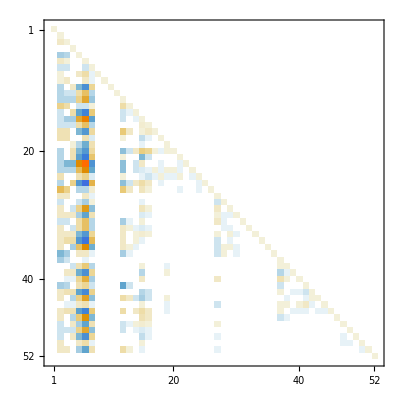

```mathematica
MatrixPlot[l]
```

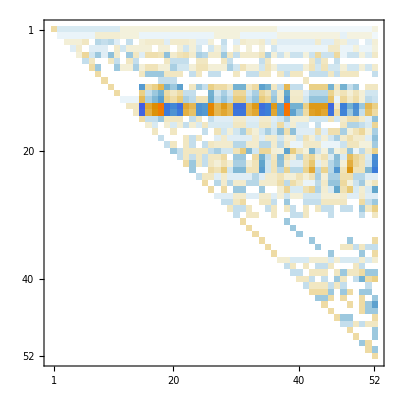

```mathematica
MatrixPlot[u]
```

```mathematica
allGraph5Atoms=Table[allGraphs5[k,"colofour"],{k,allGraphs5AtomKeys}]
```

{v1x2x3x4x5,v1x2x3x45,v1x2x35x4,v1x2x34x5,v1x2x345,v1x25x3x4,v1x25x34,v1x24x3x5,v1x24x35,v1x245x3,v1x23x4x5,v1x23x45,v1x235x4,v1x234x5,v1x2345,v15x2x3x4,v15x2x34,v15x24x3,v15x23x4,v15x234,v14x2x3x5,v14x2x35,v14x25x3,v14x23x5,v14x235,v145x2x3,v145x23,v13x2x4x5,v13x2x45,v13x25x4,v13x24x5,v13x245,v135x2x4,v135x24,v134x2x5,v134x25,v1345x2,v12x3x4x5,v12x3x45,v12x35x4,v12x34x5,v12x345,v125x3x4,v125x34,v124x3x5,v124x35,v1245x3,v123x4x5,v123x45,v1235x4,v1234x5,v12345}

```mathematica
fullCoeff[exp_]:=Table[Coefficient[exp,k],{k,allGraph5Atoms}]
```

```mathematica
convzeta=With[
{inv=Inverse[conv]},
Monitor[
Table[
First[Select[Keys[allGraphs5],fullCoeff[allGraphs5[#,"colofour"]]==inv[[kk]]&]],
{kk,1,52}
],
kk]
]
```

{0,1,9,3,243,81,27,19683,6561,2187,729,244,84,36,19684,19692,19686,6562,6642,6588,2190,2430,2214,738,972,810,13,333,273,109,26487,21951,20439,8757,7293,2917,19696,26488,21954,20448,6670,8784,7374,2460,3160,1062,364,28764,27246,22708,9490,29524}

```mathematica
Table[allGraphs5[k,"graph"],{k,convzeta}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
allGraph5NullAtoms=Table[allGraphs5[k,"colofourrealnull"],{k,allGraphs5NullAtomKeys}]
```

{n1x2x3x4x5,n12x3x4x5,n123x4x5,n1234x5,n12345,n1235x4,n123x45,n124x3x5,n1245x3,n124x35,n125x3x4,n125x34,n12x34x5,n12x345,n12x35x4,n12x3x45,n13x2x4x5,n134x2x5,n1345x2,n134x25,n135x2x4,n135x24,n13x24x5,n13x245,n13x25x4,n13x2x45,n14x2x3x5,n145x2x3,n145x23,n14x23x5,n14x235,n14x25x3,n14x2x35,n15x2x3x4,n15x23x4,n15x234,n15x24x3,n15x2x34,n1x23x4x5,n1x234x5,n1x2345,n1x235x4,n1x23x45,n1x24x3x5,n1x245x3,n1x24x35,n1x25x3x4,n1x25x34,n1x2x34x5,n1x2x345,n1x2x35x4,n1x2x3x45}

```mathematica
nullCoeff[exp_]:=Table[Coefficient[exp,k],{k,allGraph5NullAtoms}]
```

```mathematica
convzeta2=With[
{inv=Inverse[conv2]},
Monitor[
Table[
First[Select[Keys[allGraphs5],nullCoeff[allGraphs5[#,"colofourrealnull"]]==inv[[kk]]&]],
{kk,1,52}
],
kk]
]
```

{0,1,9,3,243,81,27,19683,6561,2187,729,244,84,36,19684,19692,19686,6562,6642,6588,2190,2430,2214,738,972,810,13,333,273,109,26487,21951,20439,8757,7293,2917,19696,26488,21954,20448,6670,8784,7374,2460,3160,1062,364,28764,27246,22708,9490,29524}

```mathematica
Table[allGraphs5[k,"graph"],{k,convzeta2}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
convzeta2==convzeta
```

True

```mathematica
fakeAtoms
```

```mathematica
set3=Table[allGraphs5[k,"graph"],{k,Select[Keys[allGraphs5],MemberQ[fakeAtoms,allGraphs5[#,"colofournull"]]&]}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
set3=Select[Keys[allGraphs5],MemberQ[fakeAtoms,allGraphs5[#,"colofournull"]]&]
```

{0,19683,29524,28764,27246,26487,26488,22708,21951,21954,20439,20448,19692,19696,19686,19684,6561,9490,8784,8757,7374,7293,6642,6670,6588,6562,2187,3160,2917,2430,2460,2214,2190,729,972,1062,810,738,243,364,333,273,244,81,109,84,27,36,9,13,3,1}

```mathematica
Intersection[set3,convzeta]
```

{0,1,3,9,13,27,36,81,84,109,243,244,273,333,364,729,738,810,972,1062,2187,2190,2214,2430,2460,2917,3160,6561,6562,6588,6642,6670,7293,7374,8757,8784,9490,19683,19684,19686,19692,19696,20439,20448,21951,21954,22708,26487,26488,27246,28764,29524}